# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["C:\\Users\\Miguel\\Github\\Entropy\\Symmetry sectors\\QMB_offline.wl"];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

```mathematica
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

# Translation eigenvectors

```mathematica
L=6; (*Length of the spin chain*)
dim=2^L; (*Dimension of the Hilbert space*)
basisStates=IntegerDigits[Range[0,dim-1],2,L];
```

```mathematica
TranslateState[state_List]:=RotateLeft[state];
orbits={};
visited=Association[];
Do[If[!KeyExistsQ[visited,state],orbit=NestList[TranslateState,state,L-1];
orbit=DeleteDuplicates[orbit];
(*Mark all states in the orbit as visited*)Scan[(visited[#]=True)&,orbit];
AppendTo[orbits,orbit];],{state,basisStates}];
```

```mathematica
momentumEigenstates={};
Do[orbitSize=Length[orbit];
Do[k=2 Pi m/orbitSize;
stateSum=ConstantArray[0,dim];
Do[translatedState=Nest[TranslateState,orbit[[1]],n];
index=Position[basisStates,translatedState][[1,1]];
stateSum[[index]]+=Exp[-I k n];,{n,0,orbitSize-1}];
normalizedState=stateSum/Norm[stateSum];
AppendTo[momentumEigenstates,{k,normalizedState}];,{m,0,orbitSize-1}];,{orbit,orbits}];
```

```mathematica
momentumEigenstates[[All,1]]//Sort//DeleteDuplicates
```

{0,π/3,(2 π)/3,π,(4 π)/3,(5 π)/3}

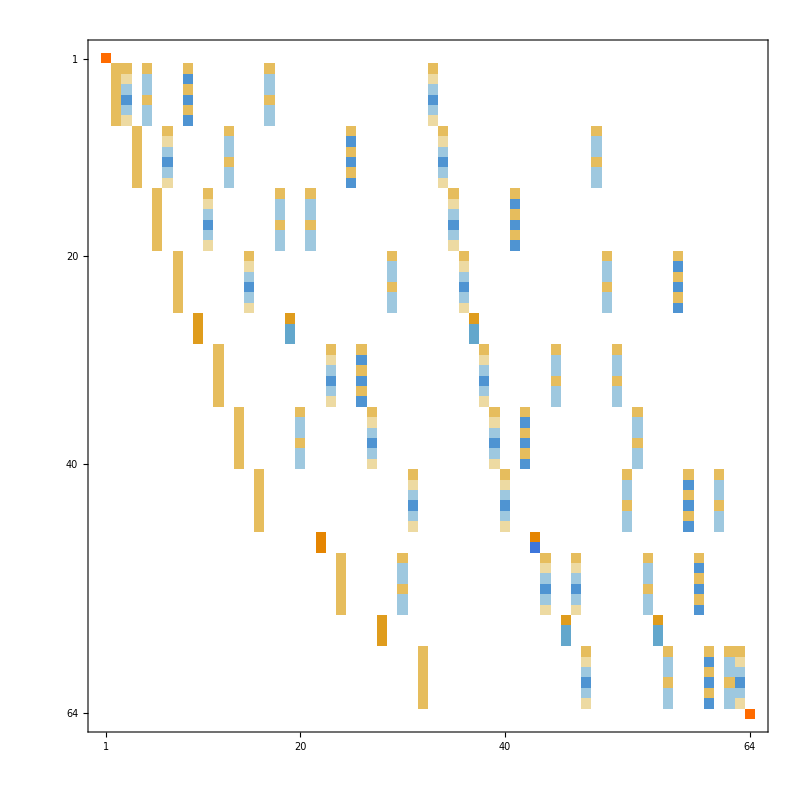

```mathematica
MatrixPlot[momentumEigenstates[[All,2]],ImageSize->800]
```

```mathematica
ks=First/@momentumEigenstates;
perm=OrderingBy[momentumEigenstates,First];
sortedKEigen=ks[[perm]];
sortedStates=(Last/@momentumEigenstates)[[perm]];
sortedPairs=Transpose[{sortedKEigen,sortedStates}];
```

```mathematica
J=1;
h=1;
g=0.5;
H=IsingNNClosedHamiltonian[h,g,J,L];
```

```mathematica
(*Assume momentumEigenstates is a list of {k,state} pairs*)
U=Transpose[sortedStates];
HMomentumBasis=ConjugateTranspose[U].H.U;
```

```mathematica
MatrixPlot[Chop[HMomentumBasis],PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
posByK=GroupBy[Range@Length[sortedKEigen],sortedKEigen[[#]]&];
blocks={};
Do[
AppendTo[blocks,HMomentumBasis[[i[[1]];;i[[-1]],i[[1]];;i[[-1]]]]];
,{i,posByK}];
val=Table[Sort[Chop[Eigenvalues[i]]],{i,blocks}];
ratios=Table[{Length[i],MeanLevelSpacingRatio[i]},{i,val}];
klist=DeleteDuplicates[ks];
```

```mathematica
ListAnimate[Table[Histogram[Differences[val[[i]]],PlotLabel->Style["dim = "<>ToString[ratios[[i,1]]]<>", k = "Text[klist[[i]]]", <r> = "<>ToString[ratios[[i,2]]],25,Black],PlotTheme->"Detailed",ImageSize->600],{i,Length[val]}],AnimationRunning->False]
```

```mathematica
glist=Range[0.01,2,0.05];
```

```mathematica
J=1;
g=1;
klist=DeleteDuplicates[ks];
```

```mathematica
alldata={};
Do[
H=IsingNNClosedHamiltonian[h,g,J,L];
U=Transpose[sortedStates];
HMomentumBasis=ConjugateTranspose[U].H.U;
posByK=GroupBy[Range@Length[sortedKEigen],sortedKEigen[[#]]&];
blocks={};
Do[
AppendTo[blocks,HMomentumBasis[[i[[1]];;i[[-1]],i[[1]];;i[[-1]]]]];
,{i,posByK}];
val=Table[Sort[Chop[Eigenvalues[i]]],{i,blocks}];
ratios=Table[{h,MeanLevelSpacingRatio[i]},{i,val}];
AppendTo[alldata,ratios];
,{h,glist}];
```

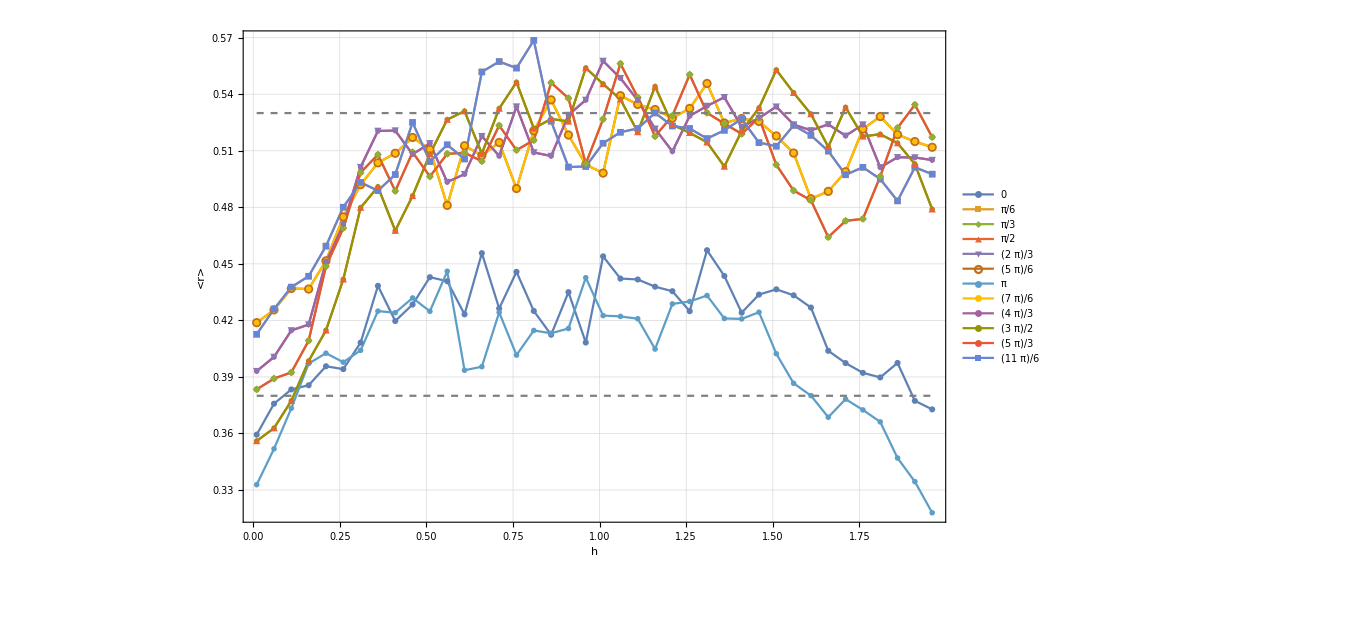

```mathematica
limits=Plot[{0.38,0.53},{x,glist[[1]],glist[[-1]]},PlotStyle->Directive[Gray,Dashed]];
Show[ListPlot[Transpose[alldata],Joined->True,PlotMarkers->Automatic,PlotLegends->Transpose[{{klist,ratios[[All,1]]}}],PlotTheme->"Detailed",FrameLabel->{Style["h",20,Black],Style["<r>",Black,20]},FrameStyle->Directive[Black,20]],limits,PlotRange->All,ImageSize->1000]
```

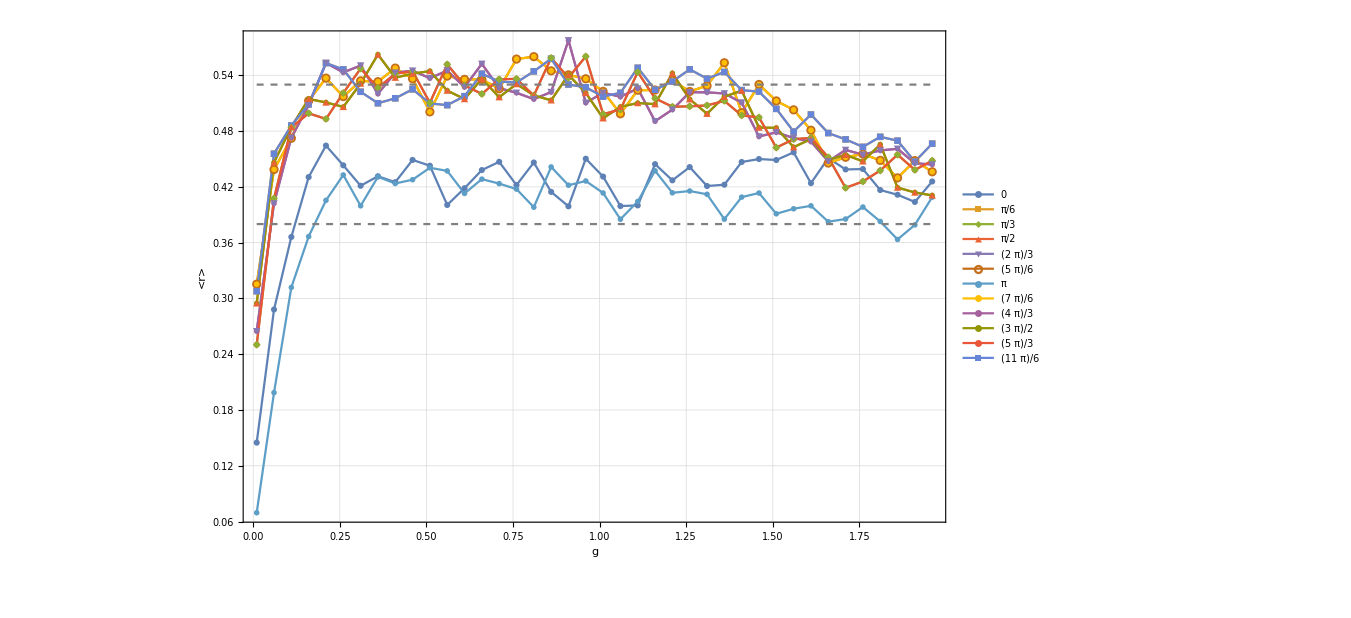

```mathematica
limits=Plot[{0.38,0.53},{x,glist[[1]],glist[[-1]]},PlotStyle->Directive[Gray,Dashed]];
Show[ListPlot[Transpose[alldata],Joined->True,PlotMarkers->Automatic,PlotLegends->Transpose[{{klist,ratios[[All,1]]}}],PlotTheme->"Detailed",FrameLabel->{Style["g",20,Black],Style["<r>",Black,20]},FrameStyle->Directive[Black,20]],limits,PlotRange->All,ImageSize->1000]
```

# Change of basis

```mathematica
L=4;
```

```mathematica
J=1;
h=1;
g=0.5;
H=IsingNNOpenHamiltonian[h,g,J,L];
```

```mathematica
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
Peven=(1/2)(IdentityMatrix[2^L]+R);
Podd=(1/2)(IdentityMatrix[2^L]-R);
```

```mathematica
uno=Table[Beven.i,{i,eveneigenvec}];
dos=Table[Bodd.i,{i,oddeigenvec}];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
```

```mathematica
newall=SortBy[Transpose[{allvals,allvecs}],First];
```

```mathematica
La=L/2;
Lb=L-La;
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,newall[[All,2]]},DistributedContexts->Full];
```

```mathematica
{eigenvalores,eigenvectores}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
fulldiag=ParallelTable[sdiag[L,La,Lb,i],{i,eigenvectores},DistributedContexts->Full];
```

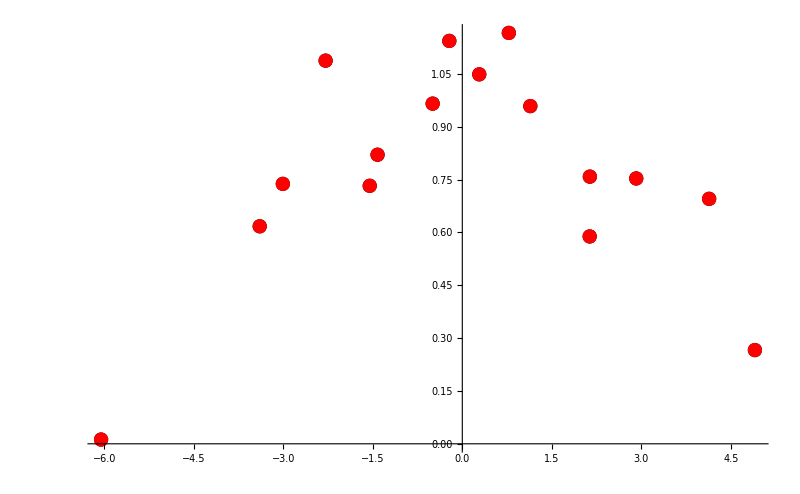

```mathematica
ListPlot[{Transpose[{eigenvalores,fulldiag}],Transpose[{newall[[All,1]],eveneigenvecdiag}]},PlotStyle->{Black,Red},PlotRange->All,ImageSize->800]
```

```mathematica
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,dima=2^(La),dimb=2^(Lb)},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

```mathematica
allstates={};
Do[
state=RandomQubitState[];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@Table[state,L/2]],Flatten[KroneckerProduct@@Table[state,L/2]]]];
AppendTo[allstates,evenini];
,{i,3}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[allvecs].i]^4],{i,allstates}];
sorted=SortBy[Transpose[{iprs,allstates}],First];
evenini=sorted[[1,2]];
```

```mathematica
evenini//TableForm
```

0.119165+0. ⅈ
0.145427-0.0760701 ⅈ
0.145427-0.0760701 ⅈ
0.128918-0.18567 ⅈ
0.145427-0.0760701 ⅈ
0.128918-0.18567 ⅈ
0.128918-0.18567 ⅈ
0.0388051-0.308885 ⅈ
0.145427-0.0760701 ⅈ
0.128918-0.18567 ⅈ
0.128918-0.18567 ⅈ
0.0388051-0.308885 ⅈ
0.128918-0.18567 ⅈ
0.0388051-0.308885 ⅈ
0.0388051-0.308885 ⅈ
-0.149823-0.401731 ⅈ

```mathematica
newini=Transpose[Beven].evenini//TableForm
```

0.119165+0. ⅈ
0.205665-0.107579 ⅈ
0.128918-0.18567 ⅈ
0.205665-0.107579 ⅈ
0.128918-0.18567 ⅈ
0.182317-0.262577 ⅈ
0.182317-0.262577 ⅈ
0.0548787-0.436829 ⅈ
0.0548787-0.436829 ⅈ
-0.149823-0.401731 ⅈ

```mathematica
MatrixPartialTrace[Dyad[evenini],2,{2^2,2^2}]//Dimensions
```

{4,4}

```mathematica
Beven//Dimensions
```

{16,10}

# Open chain even parity only

```mathematica
L=8;
```

```mathematica
J=1;
h=1;
g=4;
H=IsingNNOpenHamiltonian[h,g,J,L];
```

```mathematica
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
```

```mathematica
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
```

```mathematica
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=Table[Beven.i,{i,eveneigenvec}];
dos=Table[Bodd.i,{i,oddeigenvec}];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
```

```mathematica
La=L/2;
Lb=L-La;
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,newall[[All,2]]},DistributedContexts->Full];
```

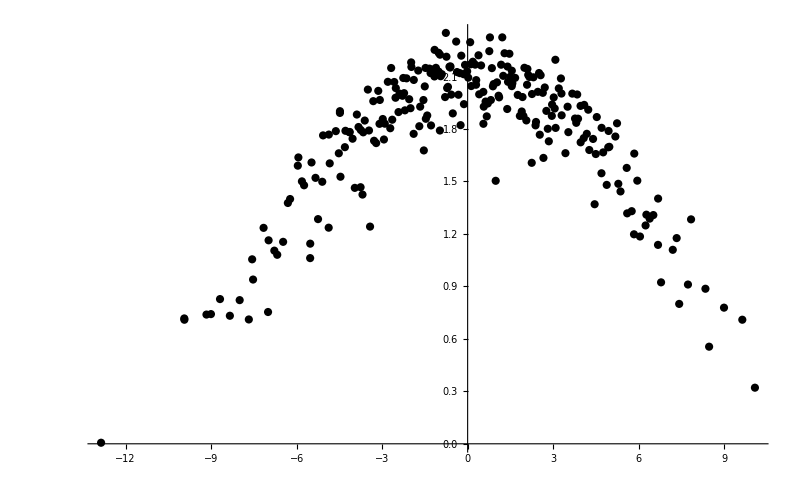

```mathematica
ListPlot[Transpose[{newall[[All,1]],eveneigenvecdiag}],PlotStyle->Black,PlotRange->All,ImageSize->800]
```

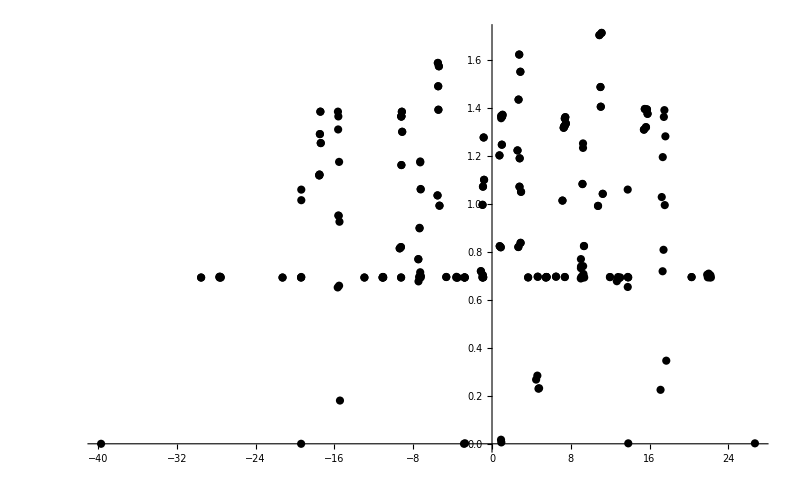

```mathematica
ListPlot[Transpose[{newall[[All,1]],eveneigenvecdiag}],PlotStyle->Black,PlotRange->All,ImageSize->800]
```

```mathematica
Peven=(1/2)(IdentityMatrix[2^L]+R);
Podd=(1/2)(IdentityMatrix[2^L]-R);
```

```mathematica
allstates={};
Do[
state=RandomQubitState[];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@Table[state,L/2]],Flatten[KroneckerProduct@@Table[state,L/2]]]];
AppendTo[allstates,evenini];
,{i,1000}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[allvecs].i]^4],{i,allstates}];
```

```mathematica
sorted=SortBy[Transpose[{iprs,allstates}],First];
```

```mathematica
evenini=sorted[[1,2]];
projected=Transpose[Beven].evenini;
```

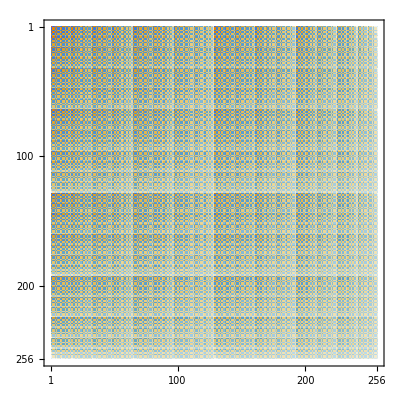

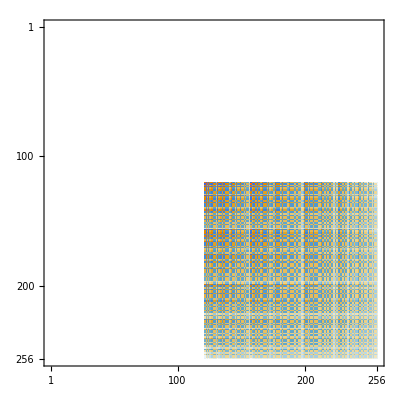

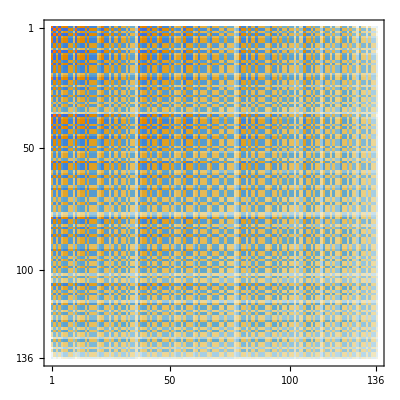

```mathematica
MatrixPlot[Dyad[evenini]]
MatrixPlot[Chop[Conjugate[evecR].Dyad[evenini].Transpose[evecR]]]
MatrixPlot[Dyad[projected]]
```

```mathematica
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
```

```mathematica
tlist=Table[10^i,{i,-2,10,0.005}];
tlist//Length
```

2401

```mathematica
data=ParallelTable[statet[eveneigenval,eveneigenvec,Beven,t,evenini],{t,tlist},DistributedContexts->Full];
```

```mathematica
data2=ParallelTable[Dyad[i],{i,data},DistributedContexts->Full];
```

```mathematica
data3=ParallelTable[Eigenvalues[i],{i,data2},DistributedContexts->Full];
```

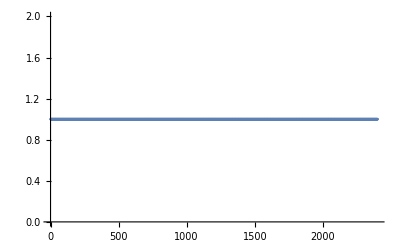

```mathematica
Table[Total[i],{i,data3}]//ListPlot
```

```mathematica
reduced=ParallelTable[MatrixPartialTrace[i,2,{2^(L/2),2^(L/2)}],{i,data2},DistributedContexts->Full];
```

```mathematica
data4=ParallelTable[Eigenvalues[Chop[i]],{i,reduced},DistributedContexts->Full];
```

-Graphics-

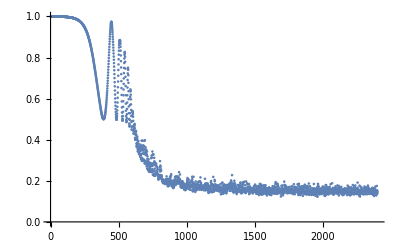

```mathematica
Table[Total[i],{i,data4}]//ListPlot
Table[Total[i^2],{i,data4}]//ListPlot
```

```mathematica
entro=Table[Chop[Total[Map[VNentropy,i]]],{i,data4}];
```

```mathematica
inieigen=Beven.Conjugate[eveneigenvec].(Transpose[Beven].evenini);
sdiagonal=Total[Map[VNentropy,Chop[Eigenvalues[MatrixPartialTrace[Dyad[inieigen],2,{2^(L/2),2^(L/2)}]]]]];
```

```mathematica
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Black,Dashed]];
diagplot=LogLinearPlot[sdiagonal,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]];
```

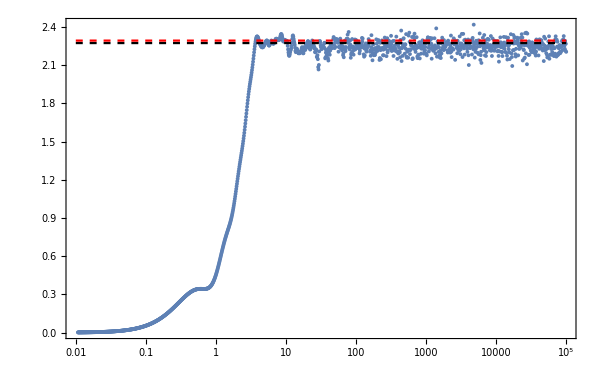

2.27487

2.29419

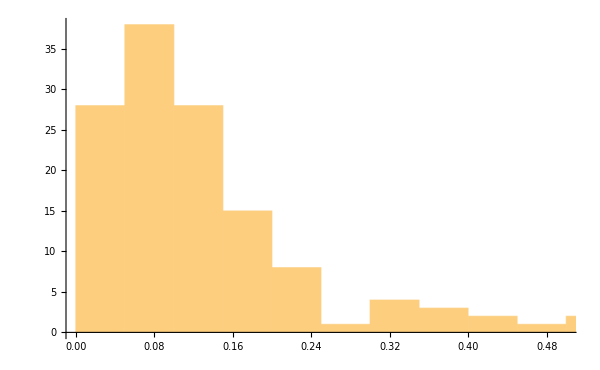

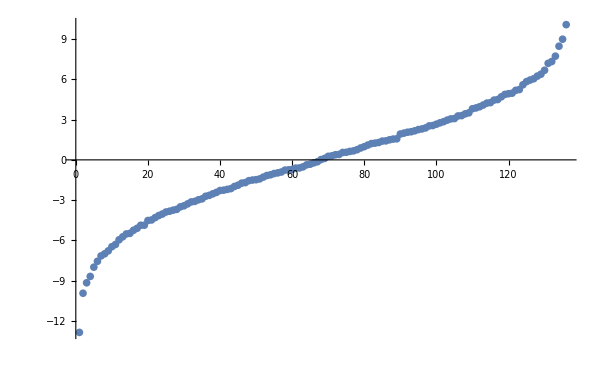

0.494574

0.569711

```mathematica
Show[{ListLogLinearPlot[Transpose[{tlist,entro}],PlotRange->All,ImageSize->600,PlotTheme->"Detailed"],pageplot,diagplot},PlotRange->All]
pageEntropy[La,Lb]//N
sdiagonal
Histogram[Differences[eveneigenval]]
ListPlot[eveneigenval]
MeanLevelSpacingRatio[eveneigenval]
MeanLevelSpacingRatio[oddeigenval]
```

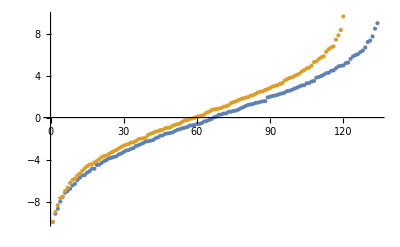

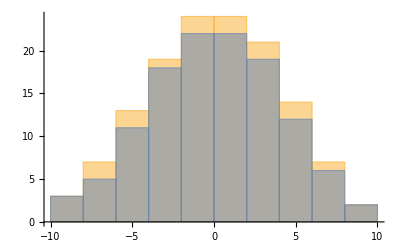

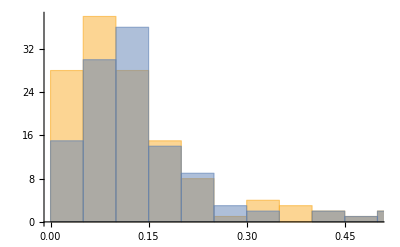

0.4964

0.569711

9181

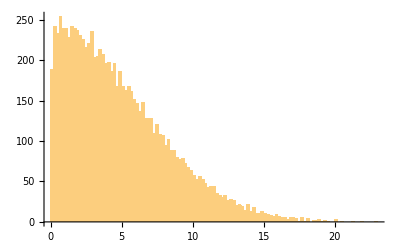

1

1

```mathematica
δ=10;
ListPlot[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]}]
Histogram[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]}]
Histogram[{Differences[eveneigenval],Differences[oddeigenval]}]
MeanLevelSpacingRatio[Select[eveneigenval,-δ<=#<=δ&]]
MeanLevelSpacingRatio[Select[oddeigenval,-δ<=#<=δ&]]
uniqueAbsDiffs=Union[Abs@Flatten@Outer[Subtract,eveneigenval,eveneigenval]];
uniqueAbsDiffs//Length
Histogram[uniqueAbsDiffs,100]
zeroCountNum=Count[Chop[uniqueAbsDiffs],0]
δ=10^-5;
zeroCountTol=Count[uniqueAbsDiffs,x_/;Abs[x]<δ]
```

## Regular

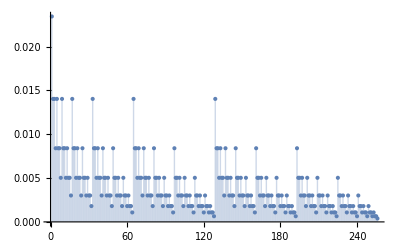

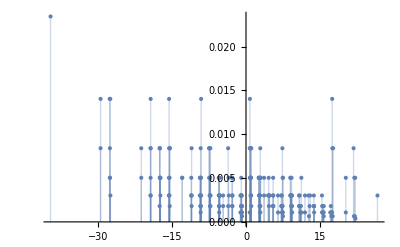

```mathematica
ListPlot[Abs[evenini]^2,PlotRange->All,Filling->Bottom]
ListPlot[Transpose[{allvals,Abs[evenini]^2}],PlotRange->All,Filling->Bottom]
```

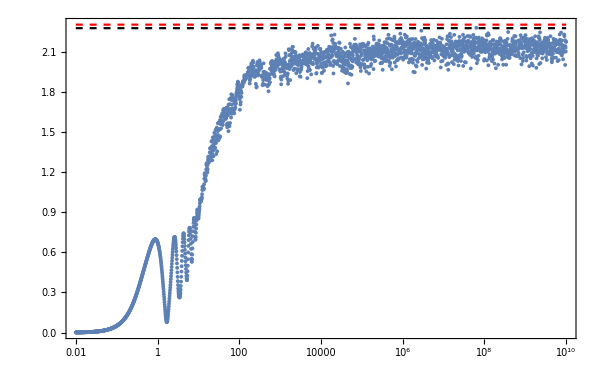

2.27487

2.3012

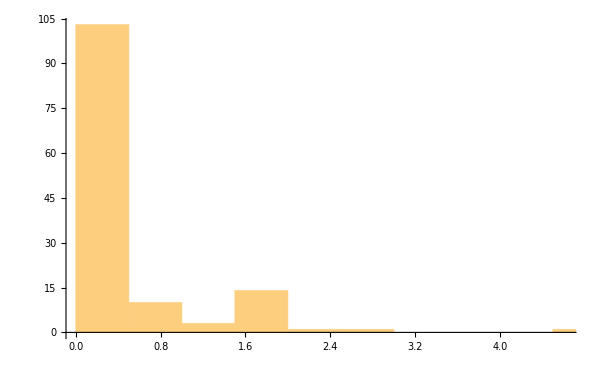

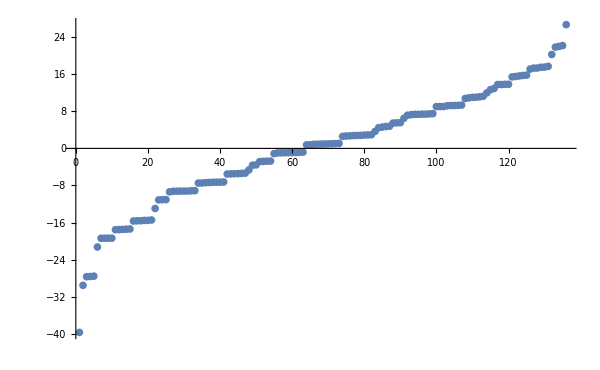

0.325849

0.348452

```mathematica
Show[{ListLogLinearPlot[Transpose[{tlist,entro}],PlotRange->All,ImageSize->600,PlotTheme->"Detailed"],pageplot,diagplot},PlotRange->All]
pageEntropy[La,Lb]//N
sdiagonal
Histogram[Differences[eveneigenval]]
ListPlot[eveneigenval]
MeanLevelSpacingRatio[eveneigenval]
MeanLevelSpacingRatio[oddeigenval]
```

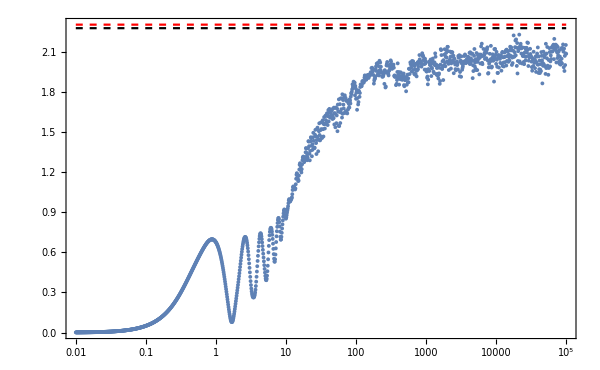

2.27487

2.3012

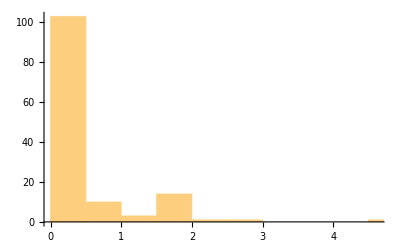

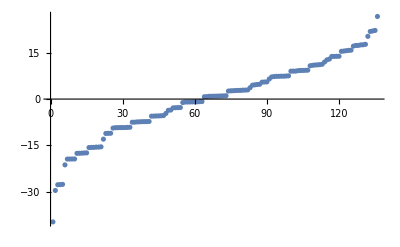

0.325849

0.348452

```mathematica
Show[{ListLogLinearPlot[Transpose[{tlist,entro}],PlotRange->All,ImageSize->600,PlotTheme->"Detailed"],pageplot,diagplot},PlotRange->All]
pageEntropy[La,Lb]//N
sdiagonal
Histogram[Differences[eveneigenval]]
ListPlot[eveneigenval]
MeanLevelSpacingRatio[eveneigenval]
MeanLevelSpacingRatio[oddeigenval]
```

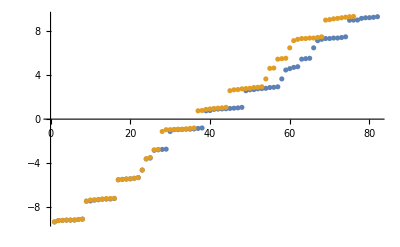

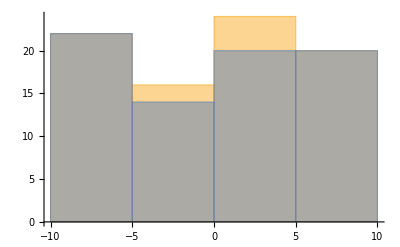

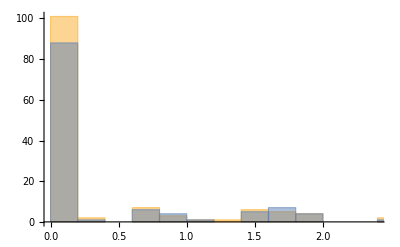

0.351544

0.35319

9181

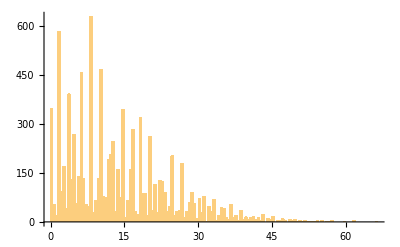

1

1

```mathematica
δ=10;
ListPlot[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]}]
Histogram[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]}]
Histogram[{Differences[eveneigenval],Differences[oddeigenval]}]
MeanLevelSpacingRatio[Select[eveneigenval,-δ<=#<=δ&]]
MeanLevelSpacingRatio[Select[oddeigenval,-δ<=#<=δ&]]
uniqueAbsDiffs=Union[Abs@Flatten@Outer[Subtract,eveneigenval,eveneigenval]];
uniqueAbsDiffs//Length
Histogram[uniqueAbsDiffs,100]
zeroCountNum=Count[Chop[uniqueAbsDiffs],0]
δ=10^-5;
zeroCountTol=Count[uniqueAbsDiffs,x_/;Abs[x]<δ]
```

# Long time S as a function of IPR

```mathematica
L=8;
```

```mathematica
J=1;
h=1;
g=1/2;
H=IsingNNOpenHamiltonian[h,g,J,L];
```

```mathematica
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
```

```mathematica
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
```

```mathematica
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=Table[Beven.i,{i,eveneigenvec}];
dos=Table[Bodd.i,{i,oddeigenvec}];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
```

```mathematica
La=L/2;
Lb=L-La;
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,newall[[All,2]]},DistributedContexts->Full];
```

```mathematica
ListPlot[Transpose[{newall[[All,1]],eveneigenvecdiag}],PlotStyle->Black,PlotRange->All,ImageSize->800]
```

-Graphics-

```mathematica
Peven=(1/2)(IdentityMatrix[2^L]+R);
Podd=(1/2)(IdentityMatrix[2^L]-R);
```

```mathematica
allstates={};
Do[
state=RandomQubitState[];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@Table[state,L/2]],Flatten[KroneckerProduct@@Table[state,L/2]]]];
AppendTo[allstates,evenini];
,{i,1000}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[allvecs].i]^4],{i,allstates}];
```

```mathematica
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
```

```mathematica
sorted=SortBy[Transpose[{iprs,allstates}],First];
```

```mathematica
evenini=sorted[[1;;-1;;100,2]];
```

```mathematica
evenini//Dimensions
```

{10,256}

```mathematica
tlist=Table[10^i,{i,-2,10,0.01}];
tlist//Length
```

1201

```mathematica
plots={};
alldiagonals={};
Do[
data=ParallelTable[statet[eveneigenval,eveneigenvec,Beven,t,j],{t,tlist},DistributedContexts->Full];
data2=ParallelTable[Dyad[i],{i,data},DistributedContexts->Full];
reduced=ParallelTable[MatrixPartialTrace[i,2,{2^(L/2),2^(L/2)}],{i,data2},DistributedContexts->Full];
data4=ParallelTable[Eigenvalues[Chop[i]],{i,reduced},DistributedContexts->Full];
entro=Table[Chop[Total[Map[VNentropy,i]]],{i,data4}];
inieigen=Beven.Conjugate[eveneigenvec].(Transpose[Beven].j);
sdiagonal=Total[Map[VNentropy,Chop[Eigenvalues[MatrixPartialTrace[Dyad[inieigen],2,{2^(L/2),2^(L/2)}]]]]];
AppendTo[alldiagonals,sdiagonal];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Black,Dashed]];
diagplot=LogLinearPlot[sdiagonal,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]];
plot=Show[{ListLogLinearPlot[Transpose[{tlist,entro}],PlotRange->All,ImageSize->600,PlotTheme->"Detailed"],pageplot,diagplot},PlotRange->All];
AppendTo[plots,plot];
,{j,evenini}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

## Chaotic

```mathematica
ListPlot[Transpose[{newall[[All,1]],eveneigenvecdiag}],PlotStyle->Black,PlotRange->All,ImageSize->800]
```

-Graphics-

```mathematica
allstates={};
Do[
state=RandomQubitState[];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@Table[state,L/2]],Flatten[KroneckerProduct@@Table[state,L/2]]]];
AppendTo[allstates,evenini];
,{i,1000}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[allvecs].i]^4],{i,allstates}];
```

```mathematica
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
```

```mathematica
sorted=SortBy[Transpose[{iprs,allstates}],First];
```

```mathematica
evenini=sorted[[1;;-1;;100,2]];
```

```mathematica
tlist=Table[10^i,{i,-2,10,0.01}];
tlist//Length
```

1201

```mathematica
plots={};
alldiagonals={};
Do[
data=ParallelTable[statet[eveneigenval,eveneigenvec,Beven,t,j],{t,tlist},DistributedContexts->Full];
data2=ParallelTable[Dyad[i],{i,data},DistributedContexts->Full];
reduced=ParallelTable[MatrixPartialTrace[i,2,{2^(L/2),2^(L/2)}],{i,data2},DistributedContexts->Full];
data4=ParallelTable[Eigenvalues[Chop[i]],{i,reduced},DistributedContexts->Full];
entro=Table[Chop[Total[Map[VNentropy,i]]],{i,data4}];
inieigen=Beven.Conjugate[eveneigenvec].(Transpose[Beven].j);
sdiagonal=Total[Map[VNentropy,Chop[Eigenvalues[MatrixPartialTrace[Dyad[inieigen],2,{2^(L/2),2^(L/2)}]]]]];
AppendTo[alldiagonals,sdiagonal];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Black,Dashed]];
diagplot=LogLinearPlot[sdiagonal,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]];
plot=Show[{ListLogLinearPlot[Transpose[{tlist,entro}],PlotRange->All,ImageSize->600,PlotTheme->"Detailed"],pageplot,diagplot},PlotRange->All];
AppendTo[plots,plot];
,{j,evenini}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

```mathematica
degeneracies=Flatten[Table[If[i!=j,Abs[i-j],Null],{i,eveneigenval},{j,eveneigenval}]];
```

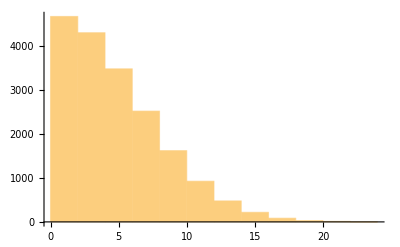

```mathematica
Histogram[degeneracies]
```

```mathematica
filter=Select[degeneracies,#<=10^-2&]
```

{0.00795663,0.00795663,0.00208618,0.00208618,0.000463846,0.000463846,0.00151646,0.00819976,0.00151646,0.0066833,0.00819976,0.0066833,0.00406389,0.00406389,0.00438934,0.00438934,0.00163393,0.00163393,0.00256637,0.00256637,0.000423548,0.000423548,0.00851152,0.00851152,0.00418196,0.00418196}

# IPR vs Sd

```mathematica
L=8;
```

```mathematica
J=1;
h=1;
g=4;
H=IsingNNOpenHamiltonian[h,g,J,L];
```

```mathematica
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
```

```mathematica
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
```

```mathematica
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=Table[Beven.i,{i,eveneigenvec}];
dos=Table[Bodd.i,{i,oddeigenvec}];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
```

```mathematica
La=L/2;
Lb=L-La;
eigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,newall[[All,2]]},DistributedContexts->Full];
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
```

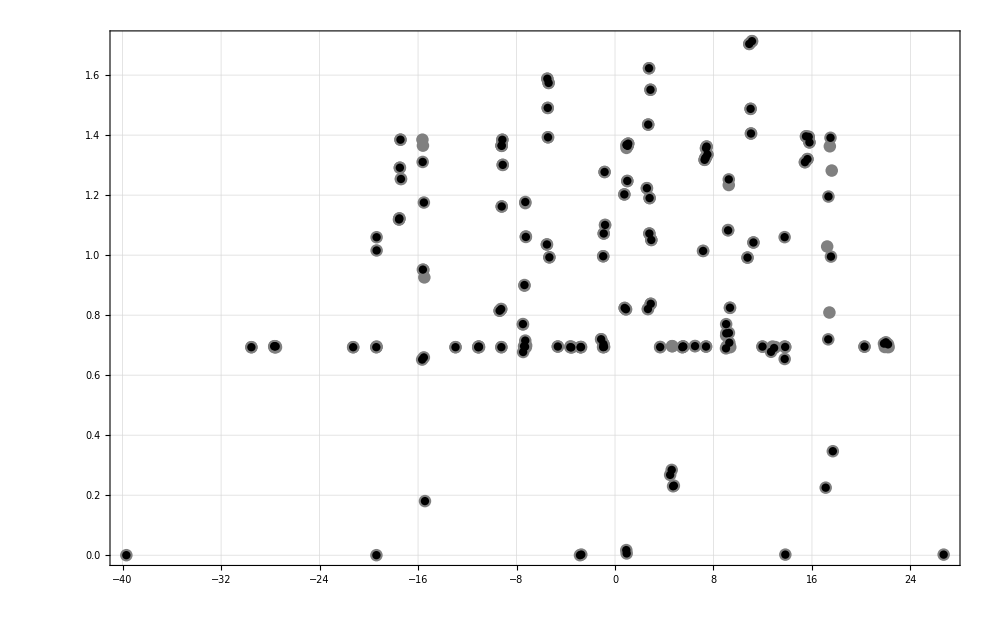

```mathematica
ListPlot[{Transpose[{newall[[All,1]],eigenvecdiag}],Transpose[{eveneigenval,eveneigenvecdiag}]},PlotStyle->{Directive[Gray,PointSize[0.009]],Directive[Black,PointSize[0.006]],Directive[Red,PointSize[0.006]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed"]
```

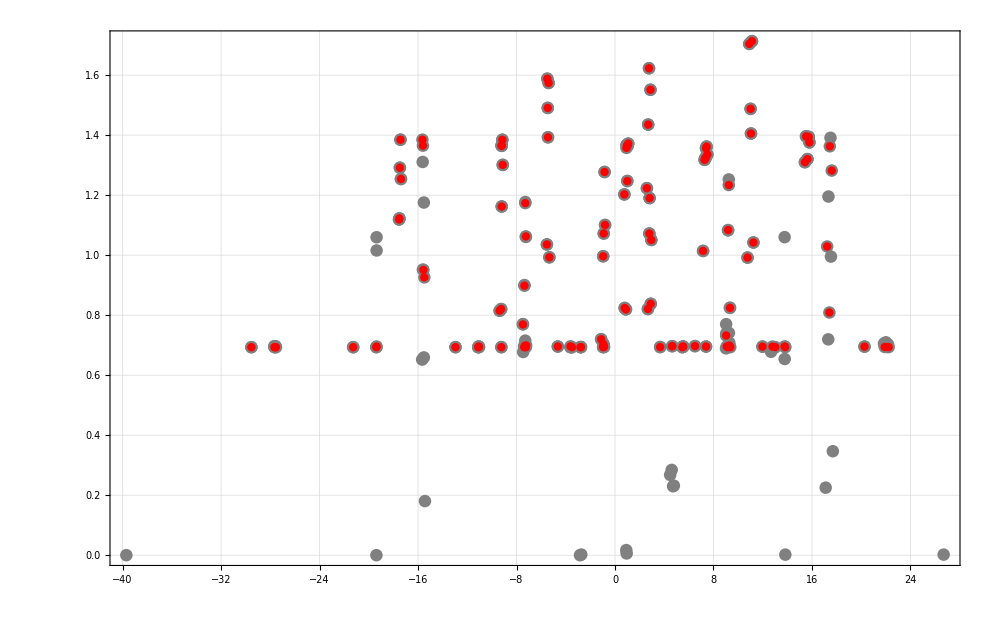

```mathematica
ListPlot[{Transpose[{newall[[All,1]],eigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Gray,PointSize[0.009]],Directive[Red,PointSize[0.006]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed"]
```

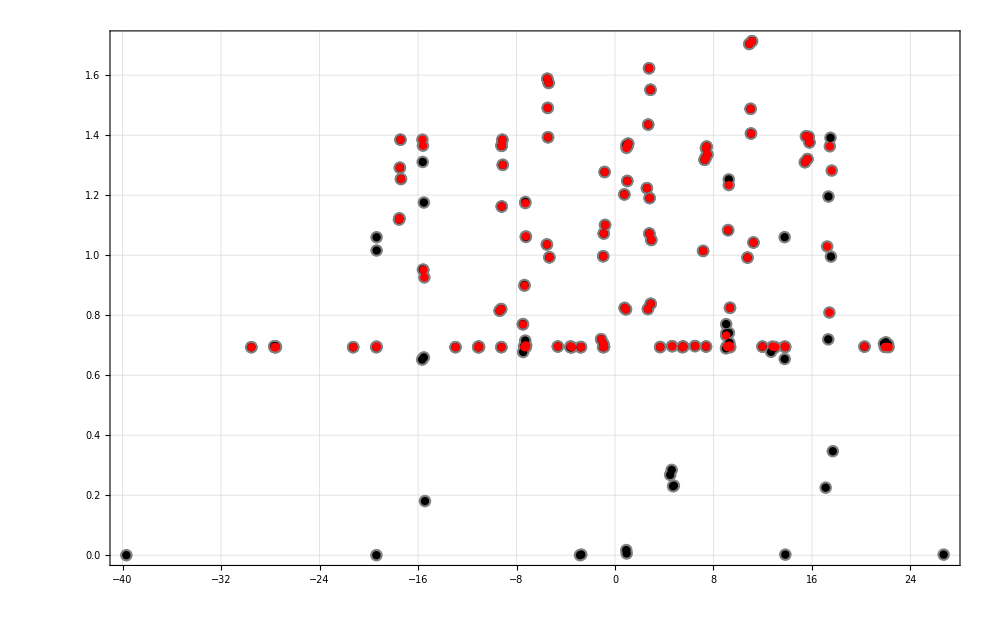

```mathematica
ListPlot[{Transpose[{newall[[All,1]],eigenvecdiag}],Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Gray,PointSize[0.009]],Directive[Black,PointSize[0.006]],Directive[Red,PointSize[0.006]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed"]
```

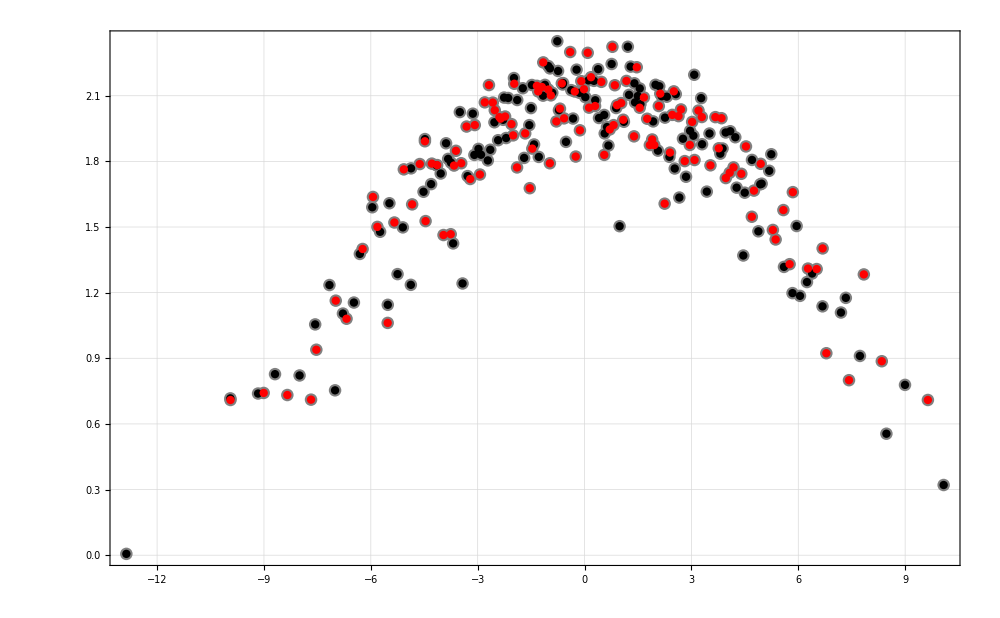

```mathematica
ListPlot[{Transpose[{newall[[All,1]],eigenvecdiag}],Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Gray,PointSize[0.009]],Directive[Black,PointSize[0.006]],Directive[Red,PointSize[0.006]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed"]
```

```mathematica
allstates={};
Do[
state=RandomQubitState[];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@Table[state,L/2]],Flatten[KroneckerProduct@@Table[state,L/2]]]];
AppendTo[allstates,evenini];
,{i,100}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[allvecs].i]^4],{i,allstates}];
```

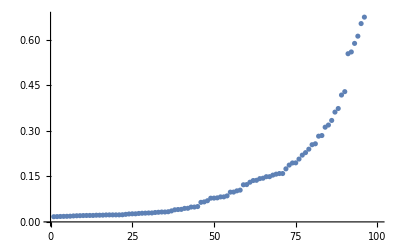

```mathematica
ListPlot[Sort[iprs]]
```

```mathematica
sorted=SortBy[Transpose[{iprs,allstates}],First];
```

```mathematica
inieigen=ParallelTable[Beven.Conjugate[eveneigenvec].(Transpose[Beven].j),{j,sorted[[All,2]]},DistributedContexts->Full];
```

```mathematica
sdiagonal=ParallelTable[Total[Map[VNentropy,Chop[Eigenvalues[MatrixPartialTrace[Dyad[j],2,{2^(L/2),2^(L/2)}]]]]],{j,inieigen},DistributedContexts->Full];
```

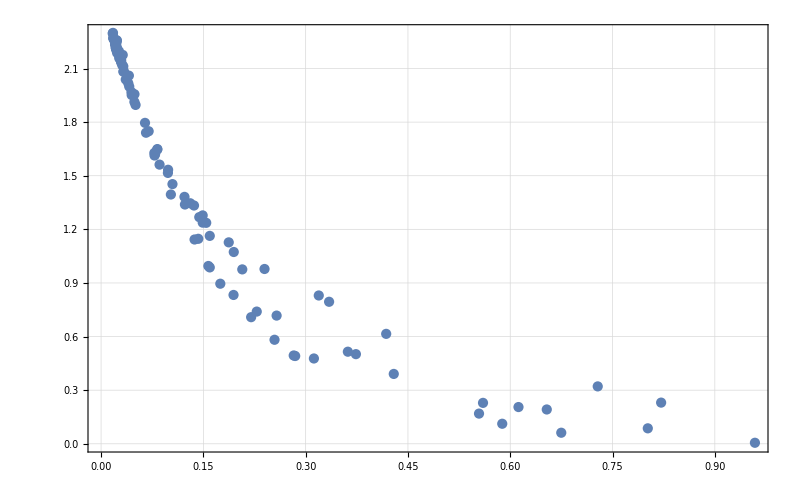

```mathematica
ListPlot[Transpose[{sorted[[All,1]],sdiagonal}],PlotRange->All,PlotTheme->"Detailed",ImageSize->800]
```

```mathematica
reducedrhos=ParallelTable[MatrixPartialTrace[Dyad[j],2,{2^(L/2),2^(L/2)}],{j,inieigen},DistributedContexts->Full];
```

```mathematica
purities=ParallelTable[Chop[Tr[i.i]],{i,reducedrhos},DistributedContexts->Full];
```

# Full random product vs even parity product h =1

## g = 0.5

```mathematica
L=10;
```

```mathematica
J=1;
h=1;
g=0.5;
H=IsingNNOpenHamiltonian[h,g,J,L];
```

```mathematica
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
```

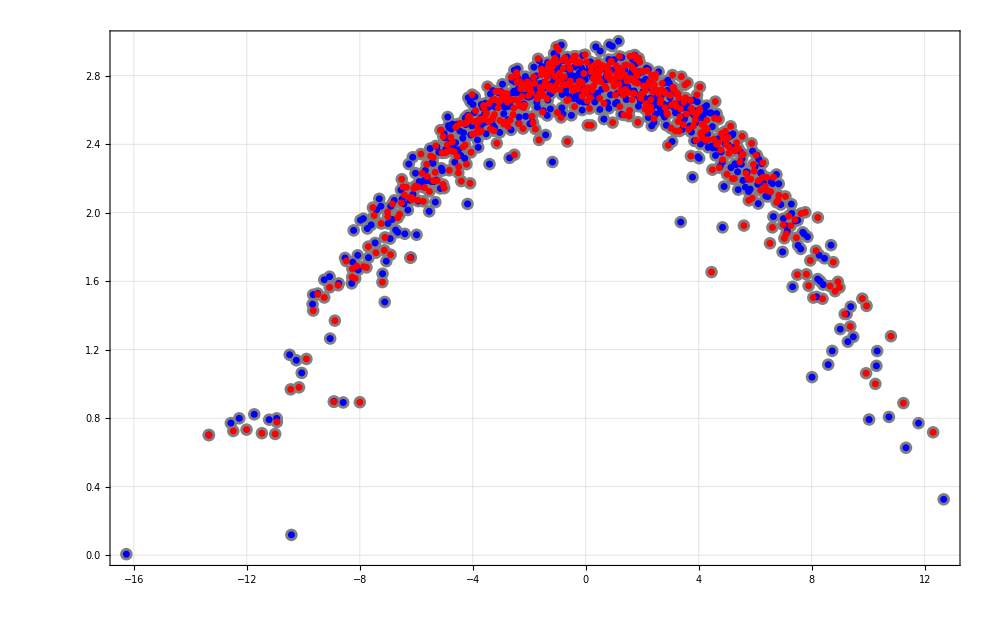

```mathematica
La=L/2;
Lb=L-La;
eigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,newall[[All,2]]},DistributedContexts->Full];
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
ListPlot[{Transpose[{newall[[All,1]],eigenvecdiag}],Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Gray,PointSize[0.009]],Directive[Blue,PointSize[0.005]],Directive[Red,PointSize[0.005]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22]]
```

```mathematica
allstates={};
Do[
state=RandomQubitState[];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@Table[state,L/2]],Flatten[KroneckerProduct@@Table[state,L/2]]]];
AppendTo[allstates,evenini];
,{i,1000}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[allvecs].i]^4],{i,allstates}];
```

```mathematica
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

```mathematica
sorted=SortBy[Transpose[{iprs,allstates}],First];
```

```mathematica
evenini=sorted[[1,2]];
```

```mathematica
tlist=Table[10^i,{i,-2,3,0.0025}];
tlist//Length
```

2001

```mathematica
entro=ParallelTable[evensvn[L,La,Lb,evenini,eveneigenval,eveneigenvec,Beven,t],{t,tlist},DistributedContexts->Full];
inieigen=Beven.Conjugate[eveneigenvec].(Transpose[Beven].evenini);
sdiagonal=Total[Map[VNentropy,Chop[Eigenvalues[MatrixPartialTrace[Dyad[inieigen],2,{2^(L/2),2^(L/2)}]]]]];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Black,Dashed]];
diagplot=LogLinearPlot[sdiagonal,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]];
```

```mathematica
plot1=ListLogLinearPlot[Transpose[{tlist,entro}],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["+ RPS",Black,30]},PlotStyle->{Directive[Blue,Opacity[0.5]]}];
```

```mathematica
productstate2=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,productstate2},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,productstate2}],First];
productstates=data[[1,2]];
svntproduct=ParallelTable[{t,svn[L,La,Lb,productstates,allvals,allvecs,t]},{t,tlist},DistributedContexts->Full];
```

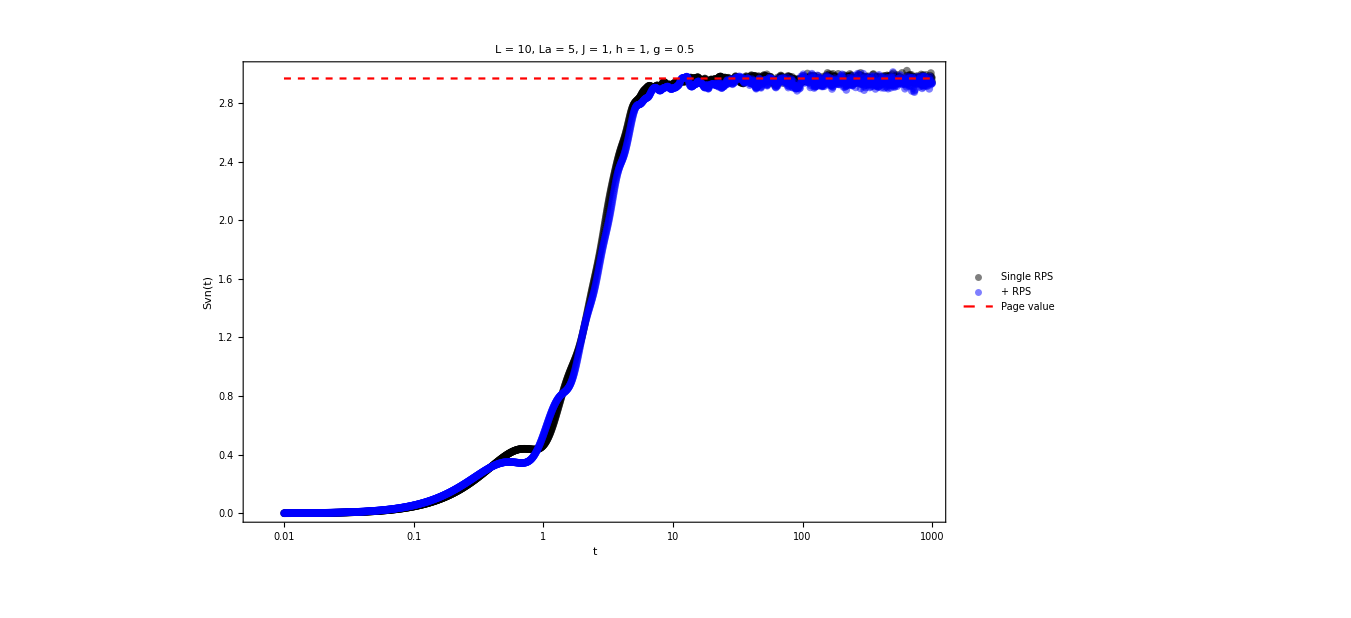

```mathematica
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Red],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Single RPS",Black,30]},PlotStyle->{Directive[Black,Opacity[0.5]]}];
Show[{svnplots,plot1,pageplot}]
```

## g = 4

```mathematica
L=8;
```

```mathematica
J=1;
h=1;
g=4;
H=IsingNNOpenHamiltonian[h,g,J,L];
```

```mathematica
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
```

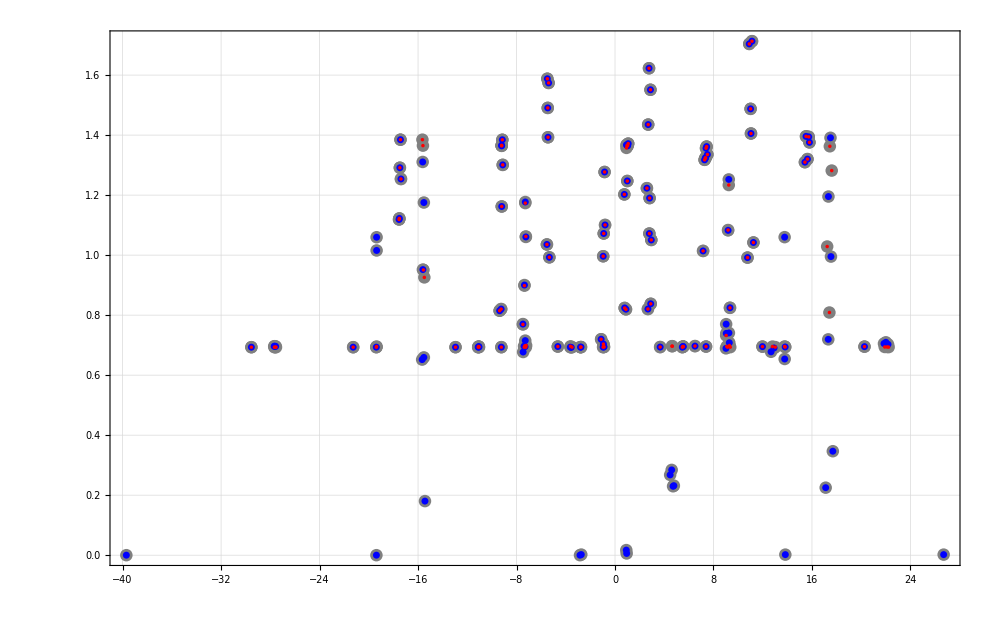

```mathematica
La=L/2;
Lb=L-La;
eigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,newall[[All,2]]},DistributedContexts->Full];
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
ListPlot[{Transpose[{newall[[All,1]],eigenvecdiag}],Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Gray,PointSize[0.009]],Directive[Blue,PointSize[0.005]],Directive[Red,PointSize[0.0025]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22]]
```

```mathematica
allstates={};
Do[
state=RandomQubitState[];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@Table[state,L/2]],Flatten[KroneckerProduct@@Table[state,L/2]]]];
AppendTo[allstates,evenini];
,{i,1000}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[allvecs].i]^4],{i,allstates}];
```

```mathematica
sorted=SortBy[Transpose[{iprs,allstates}],First];
```

```mathematica
evenini=sorted[[1,2]];
```

```mathematica
tlist=Table[10^i,{i,-2,7,0.005}];
tlist//Length
```

1801

```mathematica
entro=ParallelTable[evensvn[L,La,Lb,evenini,eveneigenval,eveneigenvec,Beven,t],{t,tlist},DistributedContexts->Full];
inieigen=Beven.Conjugate[eveneigenvec].(Transpose[Beven].evenini);
sdiagonal=Total[Map[VNentropy,Chop[Eigenvalues[MatrixPartialTrace[Dyad[inieigen],2,{2^(L/2),2^(L/2)}]]]]];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Black,Dashed]];
diagplot=LogLinearPlot[sdiagonal,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]];
```

```mathematica
plot1=ListLogLinearPlot[Transpose[{tlist,entro}],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["+ RPS",Black,30]},PlotStyle->{Directive[Blue,Opacity[0.5]]}];
```

```mathematica
productstate2=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,productstate2},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,productstate2}],First];
productstates=data[[1,2]];
svntproduct=ParallelTable[{t,svn[L,La,Lb,productstates,allvals,allvecs,t]},{t,tlist},DistributedContexts->Full];
```

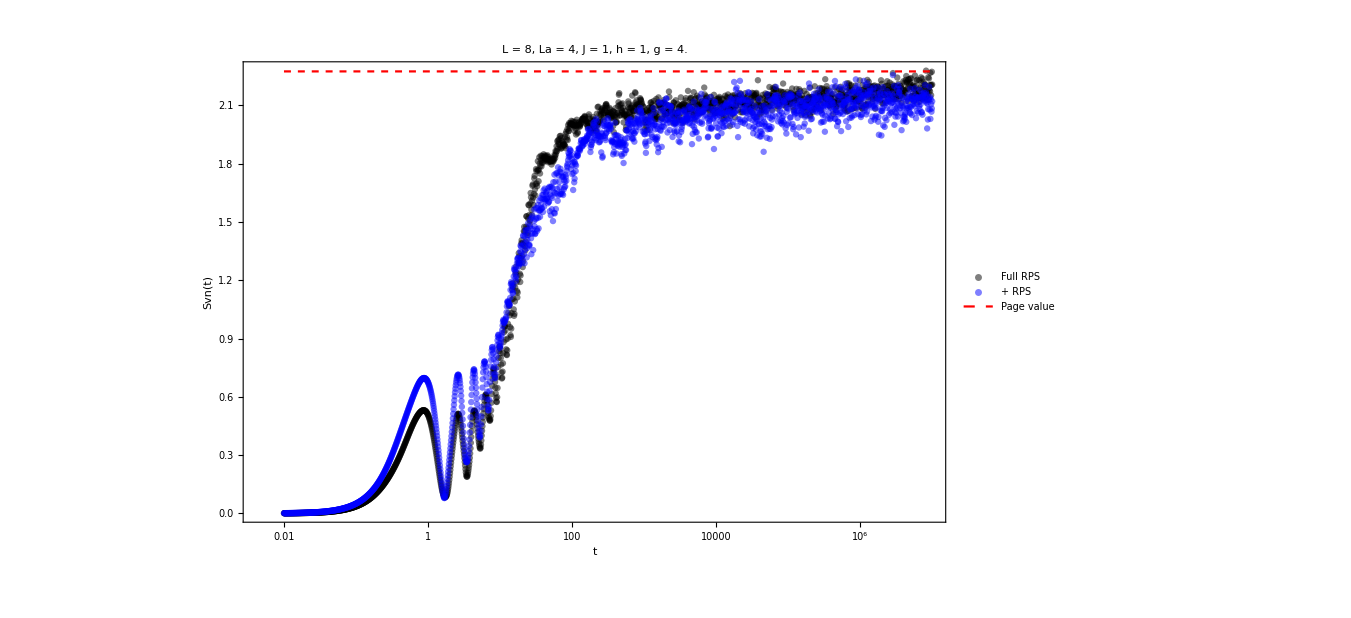

```mathematica
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Red],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Full RPS",Black,30]},PlotStyle->{Directive[Black,Opacity[0.5]]}];Show[{svnplots,plot1,pageplot}]
```

## g = 1/1000

```mathematica
L=8;
```

```mathematica
J=1;
h=1.;
g=0;
H=IsingNNOpenHamiltonian[h,g,J,L];
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
```

```mathematica
La=L/2;
Lb=L-La;
eigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,newall[[All,2]]},DistributedContexts->Full];
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
```

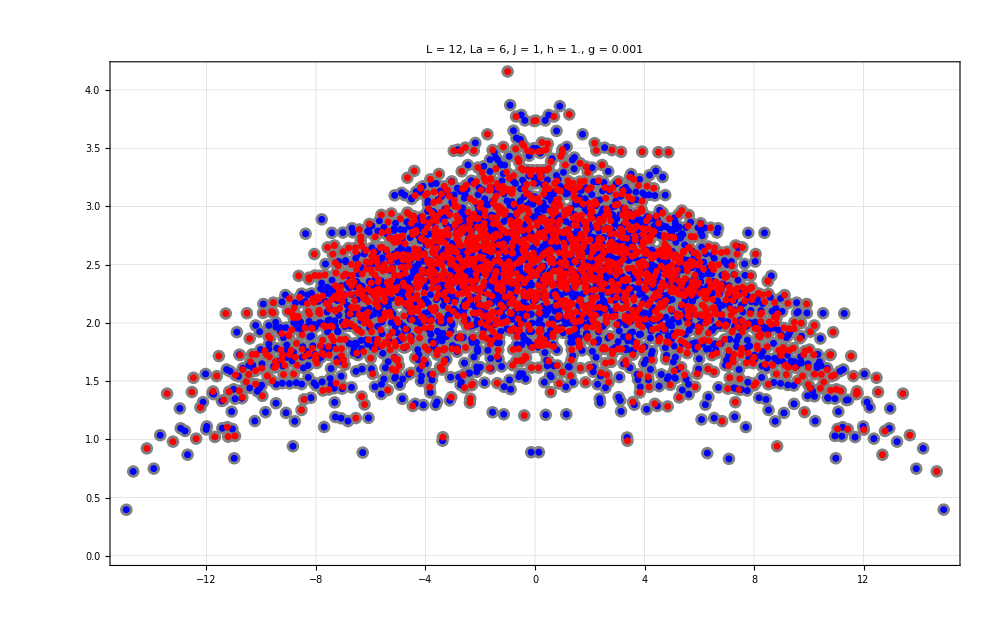

0.398327

0.384295

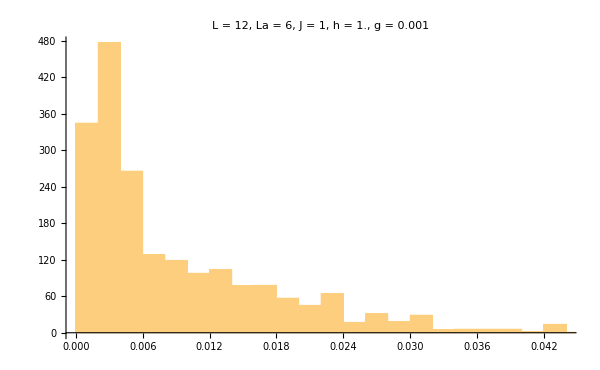

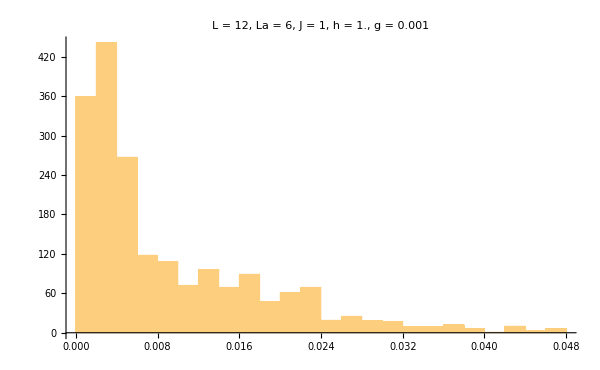

```mathematica
ListPlot[{Transpose[{newall[[All,1]],eigenvecdiag}],Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Gray,PointSize[0.009]],Directive[Blue,PointSize[0.005]],Directive[Red,PointSize[0.005]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black]]
MeanLevelSpacingRatio[Sort[eveneigenval]]
MeanLevelSpacingRatio[Sort[oddeigenval]]
Histogram[Differences[Sort[eveneigenval]],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],ImageSize->600]
Histogram[Differences[Sort[oddeigenval]],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],ImageSize->600]
```

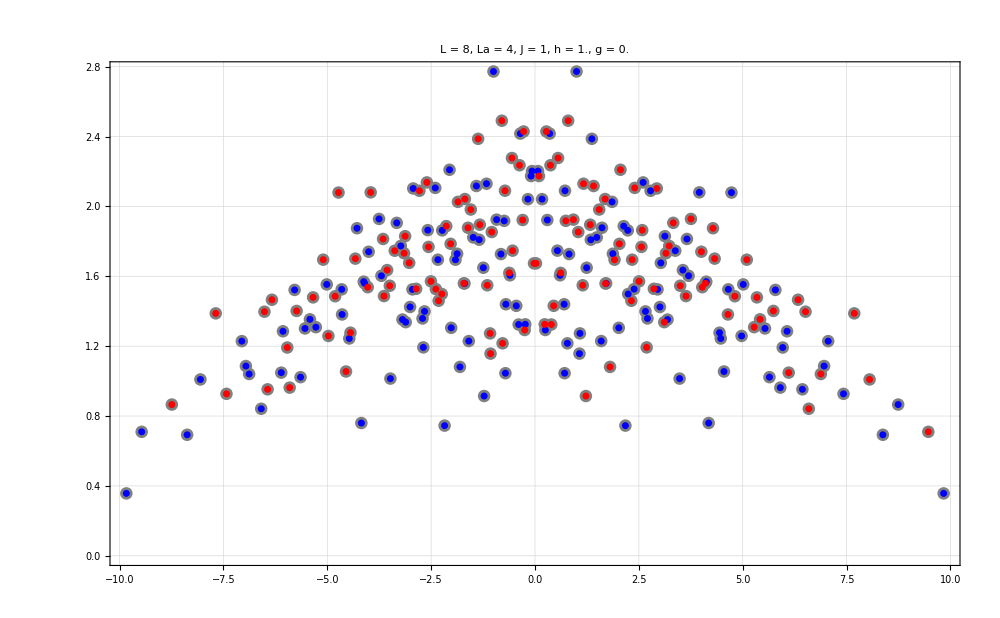

0.457164

0.454894

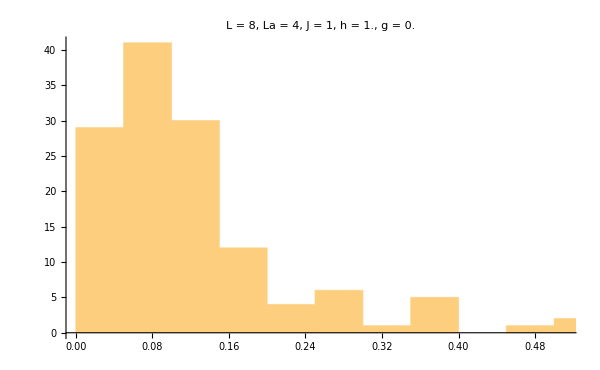

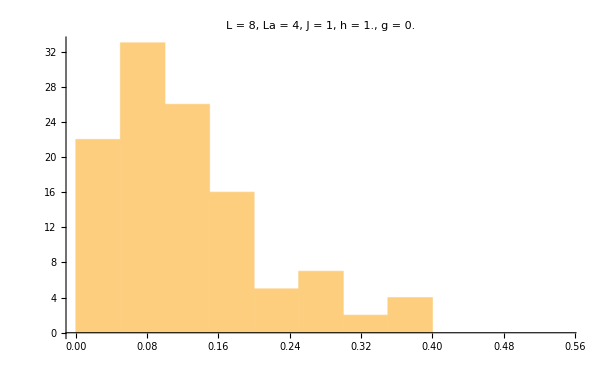

```mathematica
ListPlot[{Transpose[{newall[[All,1]],eigenvecdiag}],Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Gray,PointSize[0.009]],Directive[Blue,PointSize[0.005]],Directive[Red,PointSize[0.005]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black]]
MeanLevelSpacingRatio[Sort[eveneigenval]]
MeanLevelSpacingRatio[Sort[oddeigenval]]
Histogram[Differences[Sort[eveneigenval]],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],ImageSize->600]
Histogram[Differences[Sort[oddeigenval]],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],ImageSize->600]
```

```mathematica
allstates={};
Do[
state=RandomQubitState[];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@Table[state,L/2]],Flatten[KroneckerProduct@@Table[state,L/2]]]];
AppendTo[allstates,evenini];
,{i,1000}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[allvecs].i]^4],{i,allstates}];
```

```mathematica
sorted=SortBy[Transpose[{iprs,allstates}],First];
```

```mathematica
evenini=sorted[[1,2]];
```

```mathematica
tlist=Table[10^i,{i,-2,8,0.0025}];
tlist//Length
```

4001

```mathematica
entro=ParallelTable[evensvn[L,La,Lb,evenini,eveneigenval,eveneigenvec,Beven,t],{t,tlist},DistributedContexts->Full];
inieigen=Beven.Conjugate[eveneigenvec].(Transpose[Beven].evenini);
sdiagonal=Total[Map[VNentropy,Chop[Eigenvalues[MatrixPartialTrace[Dyad[inieigen],2,{2^(L/2),2^(L/2)}]]]]];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Black,Dashed]];
diagplot=LogLinearPlot[sdiagonal,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]];
```

```mathematica
plot1=ListLogLinearPlot[Transpose[{tlist,entro}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["+ RPS",Black,30]},PlotStyle->{Directive[Blue,Opacity[0.5]]}];
```

```mathematica
productstate2=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,productstate2},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,productstate2}],First];
productstates=data[[1,2]];
svntproduct=ParallelTable[{t,svn[L,La,Lb,productstates,allvals,allvecs,t]},{t,tlist},DistributedContexts->Full];
```

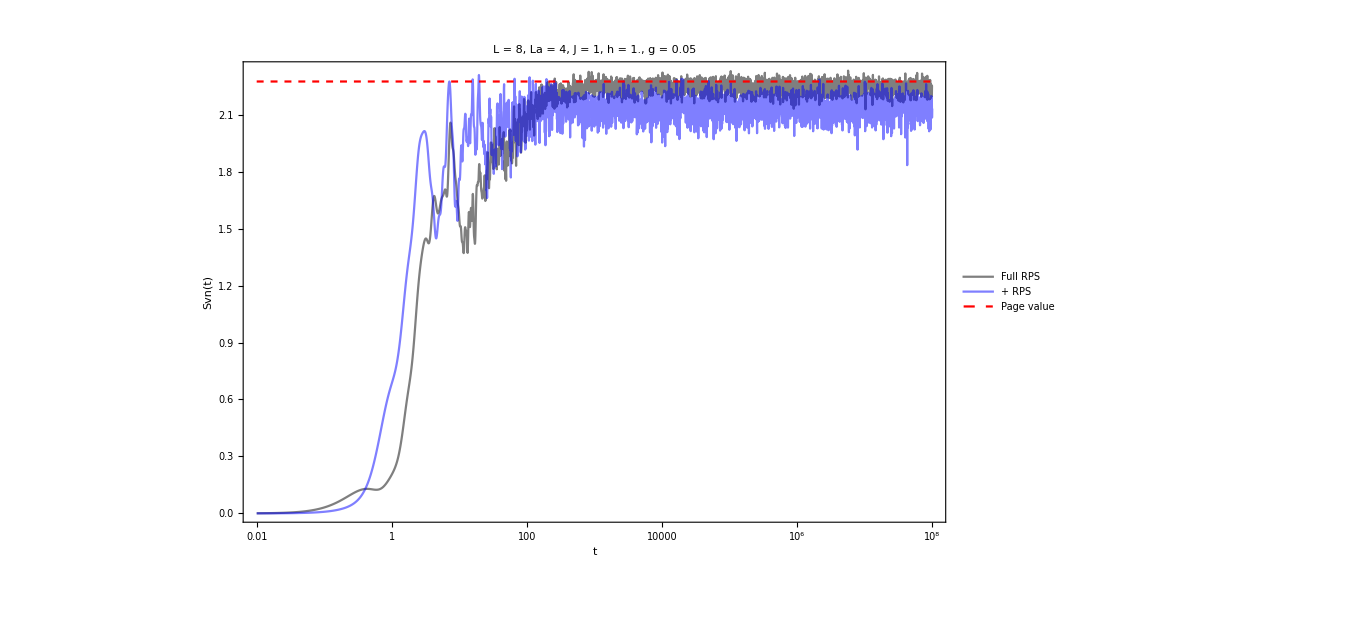

```mathematica
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Red],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Full RPS",Black,30]},PlotStyle->{Directive[Black,Opacity[0.5]]}];Show[{svnplots,plot1,pageplot},PlotRange->All]
```

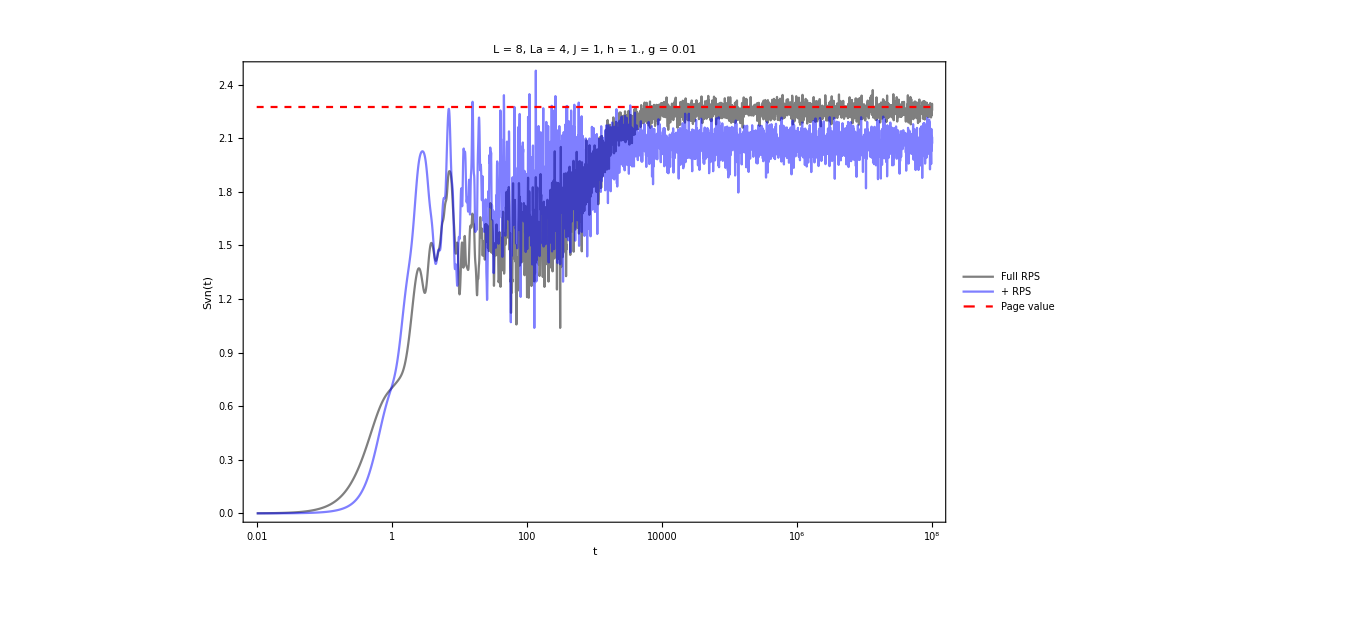

```mathematica
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Red],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Full RPS",Black,30]},PlotStyle->{Directive[Black,Opacity[0.5]]}];Show[{svnplots,plot1,pageplot},PlotRange->All]
```

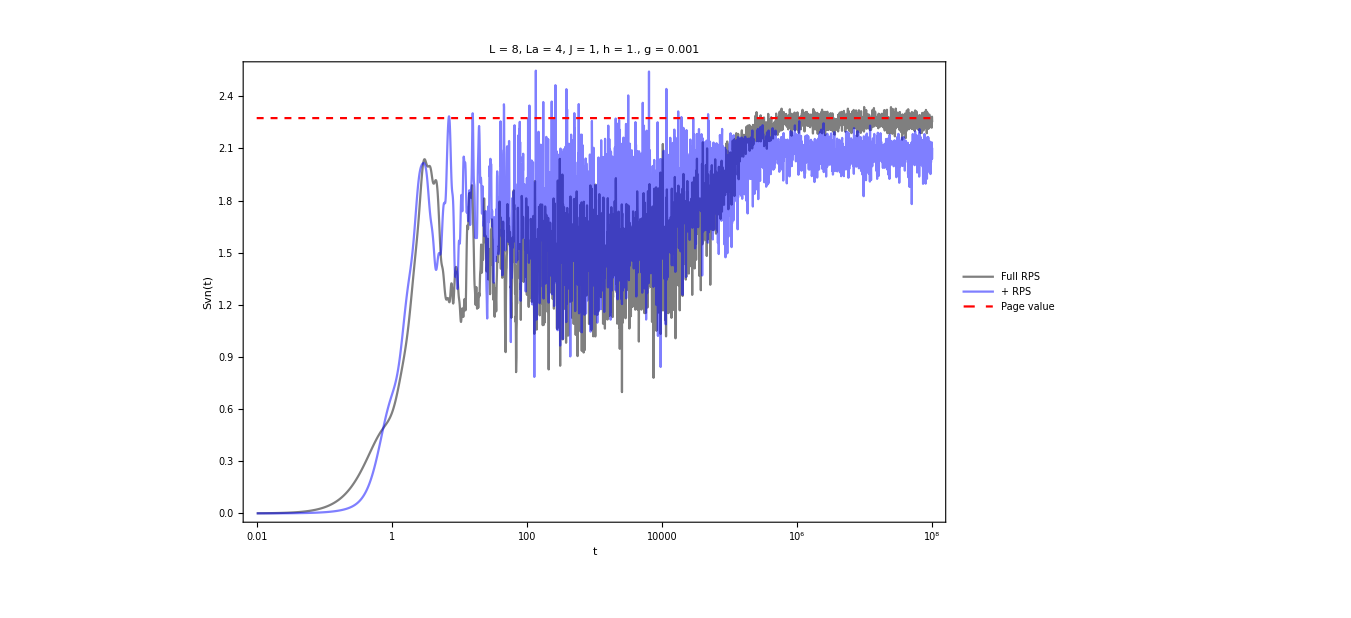

```mathematica
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Red],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Full RPS",Black,30]},PlotStyle->{Directive[Black,Opacity[0.5]]}];Show[{svnplots,plot1,pageplot},PlotRange->All]
```

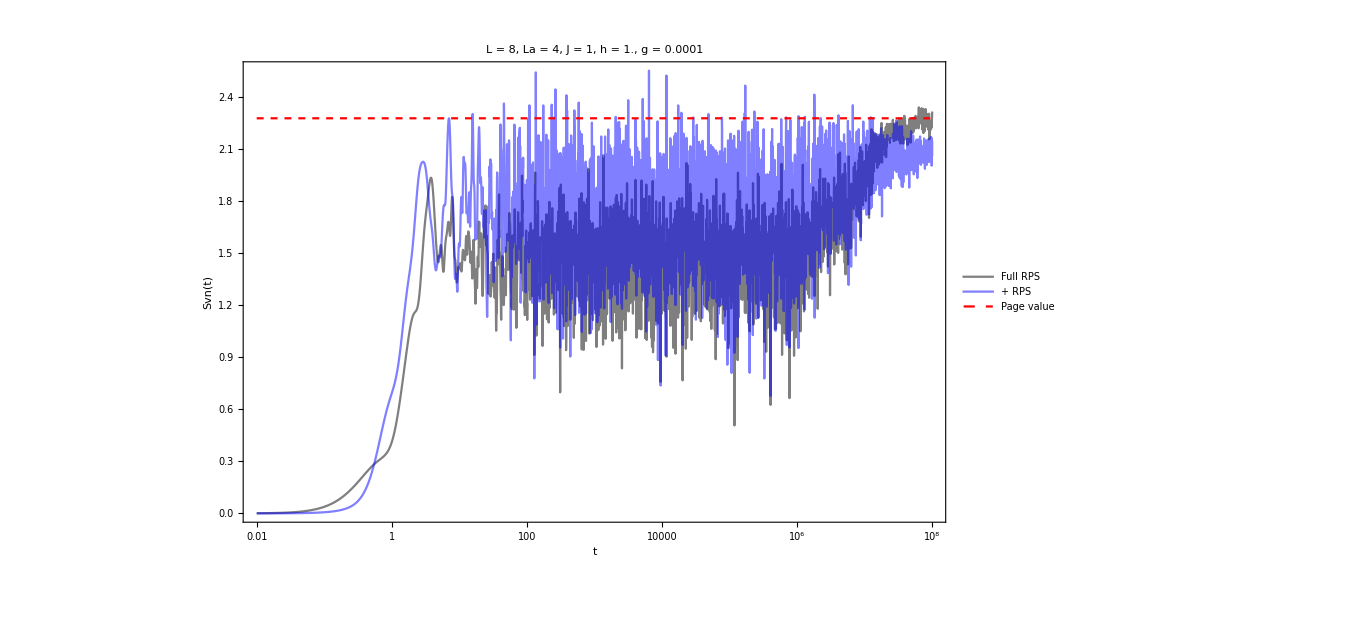

```mathematica
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Red],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Full RPS",Black,30]},PlotStyle->{Directive[Black,Opacity[0.5]]}];Show[{svnplots,plot1,pageplot},PlotRange->All]
```

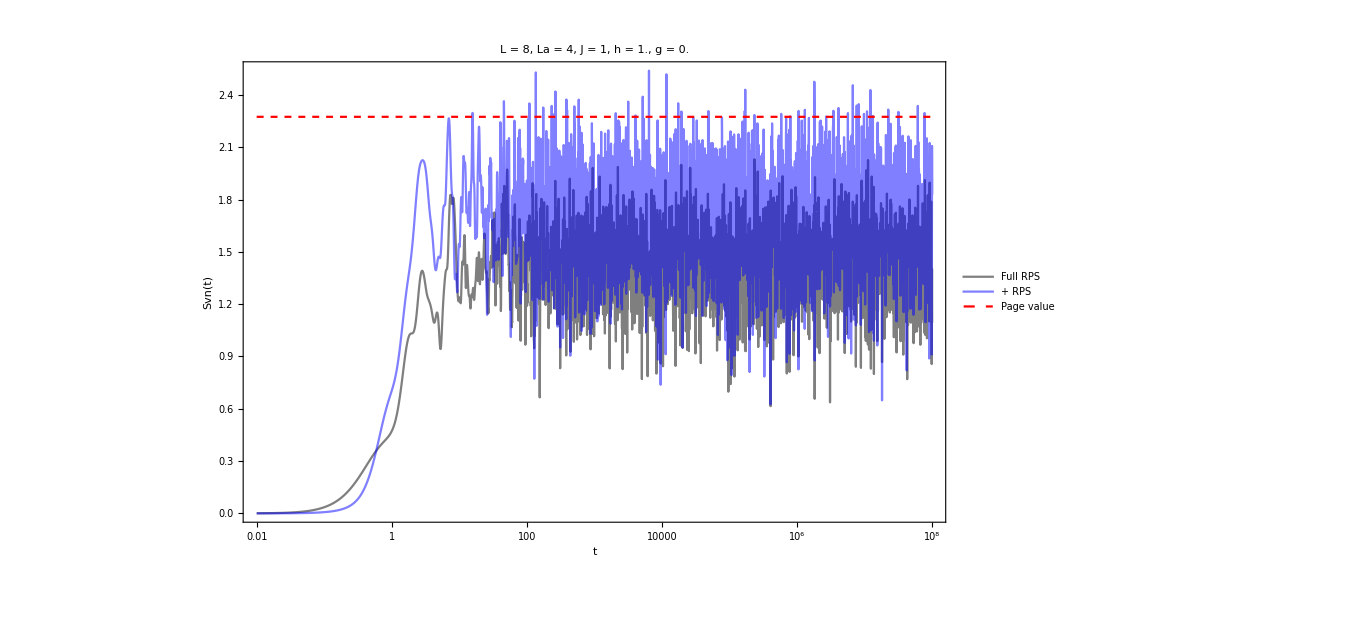

```mathematica
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Red],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Full RPS",Black,30]},PlotStyle->{Directive[Black,Opacity[0.5]]}];Show[{svnplots,plot1,pageplot},PlotRange->All]
```

# Full random product vs even parity product g =1

## h = 1.5

```mathematica
L=8;
```

```mathematica
J=1;
h=1.5;
g=1;
H=IsingNNOpenHamiltonian[h,g,J,L];
```

```mathematica
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
```

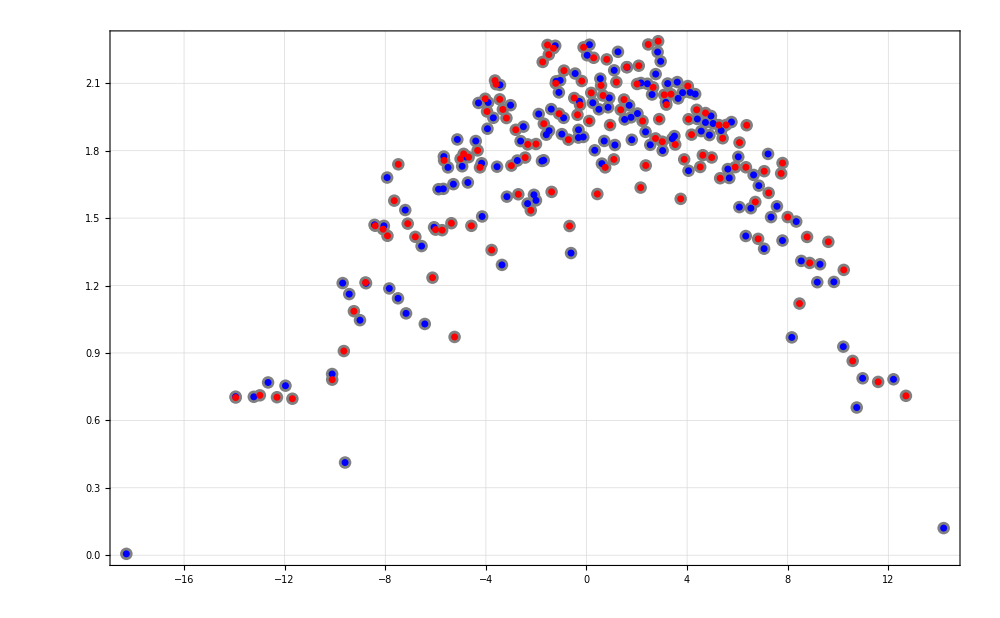

```mathematica
La=L/2;
Lb=L-La;
eigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,newall[[All,2]]},DistributedContexts->Full];
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
ListPlot[{Transpose[{newall[[All,1]],eigenvecdiag}],Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Gray,PointSize[0.009]],Directive[Blue,PointSize[0.005]],Directive[Red,PointSize[0.005]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22]]
```

```mathematica
allstates={};
Do[
state=RandomQubitState[];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@Table[state,L/2]],Flatten[KroneckerProduct@@Table[state,L/2]]]];
AppendTo[allstates,evenini];
,{i,1000}];
iprs=ParallelTable[Total[Abs[Conjugate[allvecs].i]^4],{i,allstates}];
sorted=SortBy[Transpose[{iprs,allstates}],First];
evenini=sorted[[1,2]];
```

```mathematica
tlist=Table[10^i,{i,-2,5,0.0025}];
tlist//Length
```

2801

```mathematica
entro=ParallelTable[evensvn[L,La,Lb,evenini,eveneigenval,eveneigenvec,Beven,t],{t,tlist},DistributedContexts->Full];
inieigen=Beven.Conjugate[eveneigenvec].(Transpose[Beven].evenini);
sdiagonal=Total[Map[VNentropy,Chop[Eigenvalues[MatrixPartialTrace[Dyad[inieigen],2,{2^(L/2),2^(L/2)}]]]]];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Black,Dashed]];
diagplot=LogLinearPlot[sdiagonal,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]];
```

```mathematica
plot1=ListLogLinearPlot[Transpose[{tlist,entro}],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["+ RPS",Black,30]},PlotStyle->{Directive[Blue,Opacity[0.5]]}];
```

```mathematica
productstate2=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,productstate2},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,productstate2}],First];
productstates=data[[1,2]];
svntproduct=ParallelTable[{t,svn[L,La,Lb,productstates,allvals,allvecs,t]},{t,tlist},DistributedContexts->Full];
```

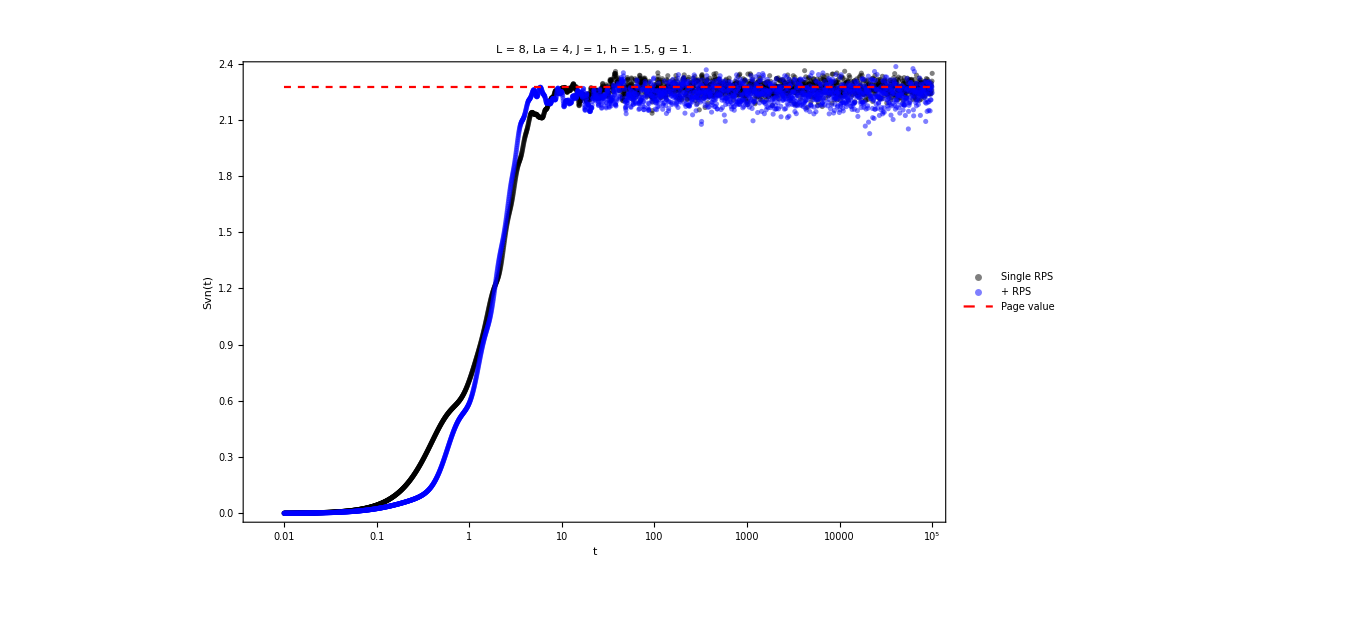

```mathematica
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Red],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Single RPS",Black,30]},PlotStyle->{Directive[Black,Opacity[0.5]]}];
Show[{svnplots,plot1,pageplot}]
```

## h = 0.1

```mathematica
L=8;
```

```mathematica
J=1;
h=1/10;
g=1;
H=IsingNNOpenHamiltonian[h,g,J,L];
```

```mathematica
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
```

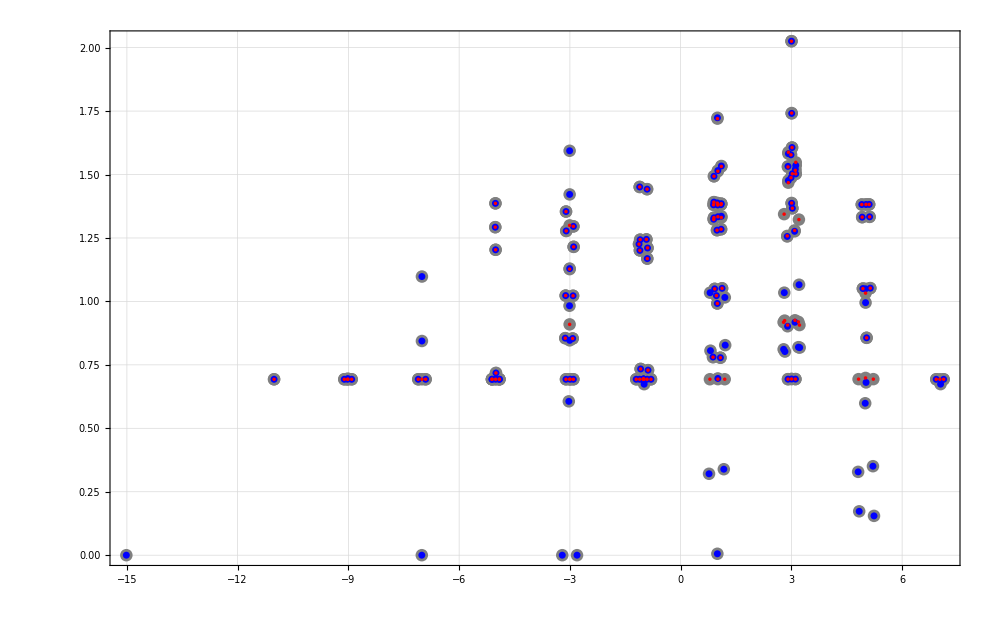

```mathematica
La=L/2;
Lb=L-La;
eigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,newall[[All,2]]},DistributedContexts->Full];
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
ListPlot[{Transpose[{newall[[All,1]],eigenvecdiag}],Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Gray,PointSize[0.009]],Directive[Blue,PointSize[0.005]],Directive[Red,PointSize[0.0025]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22]]
```

```mathematica
allstates={};
Do[
state=RandomQubitState[];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@Table[state,L/2]],Flatten[KroneckerProduct@@Table[state,L/2]]]];
AppendTo[allstates,evenini];
,{i,1000}];
iprs=ParallelTable[Total[Abs[Conjugate[allvecs].i]^4],{i,allstates}];
sorted=SortBy[Transpose[{iprs,allstates}],First];
evenini=sorted[[1,2]];
```

```mathematica
tlist=Table[10^i,{i,-2,6,0.0025}];
tlist//Length
```

3201

```mathematica
entro=ParallelTable[evensvn[L,La,Lb,evenini,eveneigenval,eveneigenvec,Beven,t],{t,tlist},DistributedContexts->Full];
inieigen=Beven.Conjugate[eveneigenvec].(Transpose[Beven].evenini);
sdiagonal=Total[Map[VNentropy,Chop[Eigenvalues[MatrixPartialTrace[Dyad[inieigen],2,{2^(L/2),2^(L/2)}]]]]];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Black,Dashed]];
diagplot=LogLinearPlot[sdiagonal,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]];
```

```mathematica
plot1=ListLogLinearPlot[Transpose[{tlist,entro}],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["+ RPS",Black,30]},PlotStyle->{Directive[Blue,Opacity[0.5]]}];
```

```mathematica
productstate2=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,productstate2},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,productstate2}],First];
productstates=data[[1,2]];
svntproduct=ParallelTable[{t,svn[L,La,Lb,productstates,allvals,allvecs,t]},{t,tlist},DistributedContexts->Full];
```

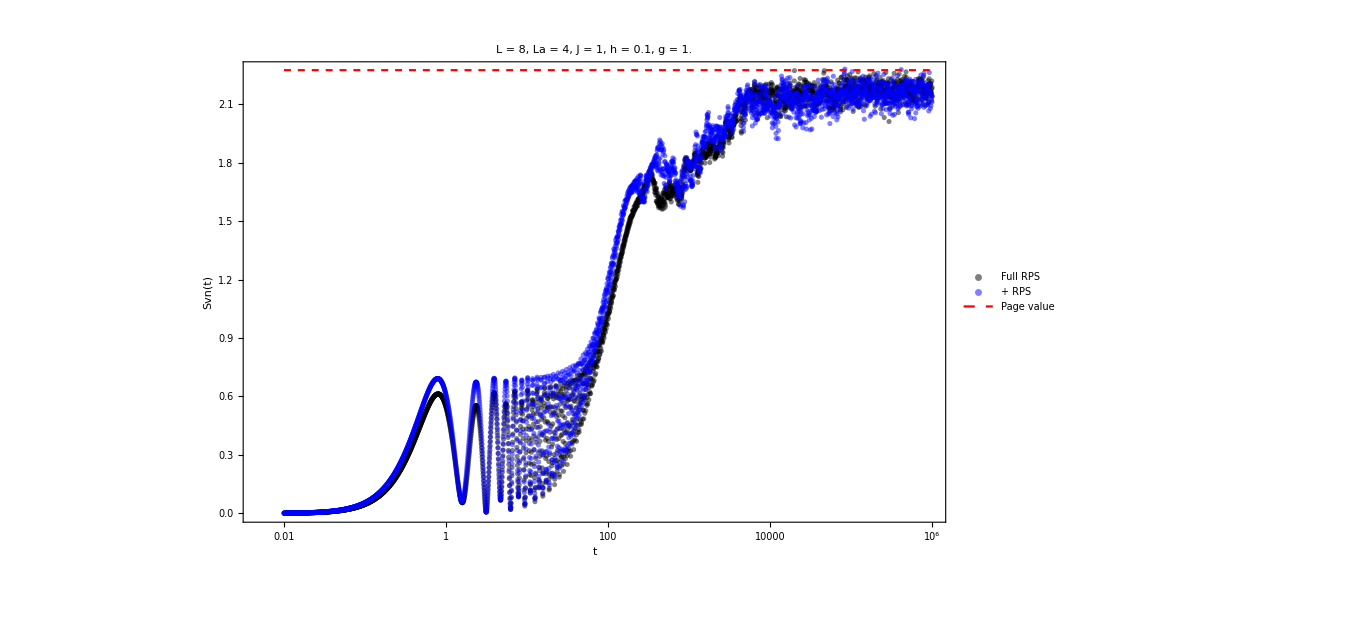

```mathematica
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Red],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Full RPS",Black,30]},PlotStyle->{Directive[Black,Opacity[0.5]]}];Show[{svnplots,plot1,pageplot}]
```

## h=0.01

```mathematica
L=10;
```

```mathematica
J=1;
h=0.01;
g=1;
H=IsingNNOpenHamiltonian[h,g,J,L];
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
```

```mathematica
La=L/2;
Lb=L-La;
eigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,newall[[All,2]]},DistributedContexts->Full];
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
```

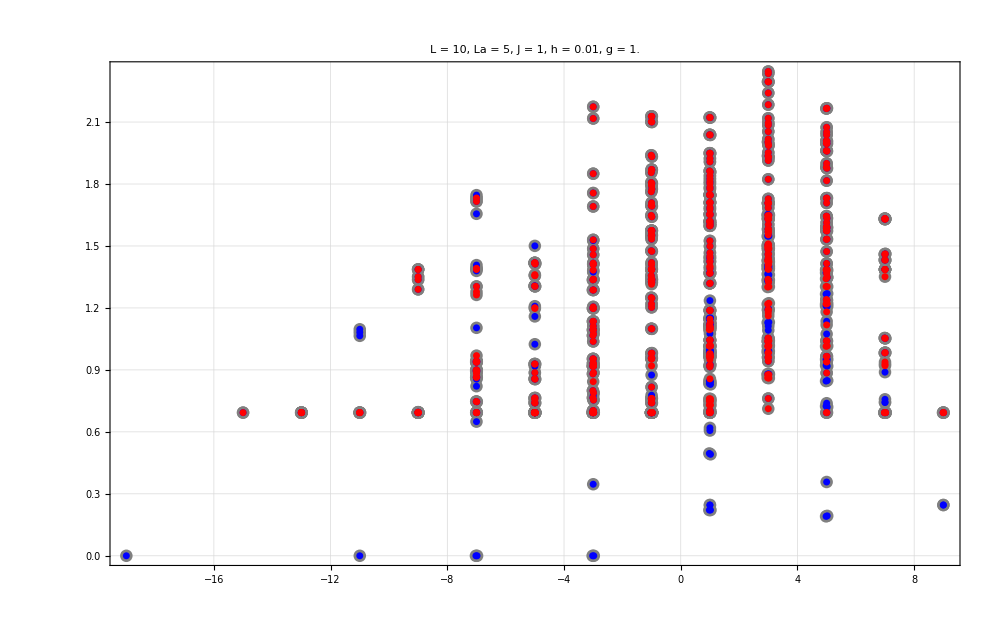

0.328729

0.313471

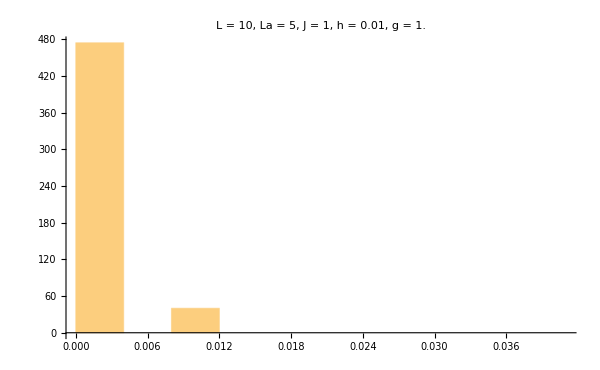

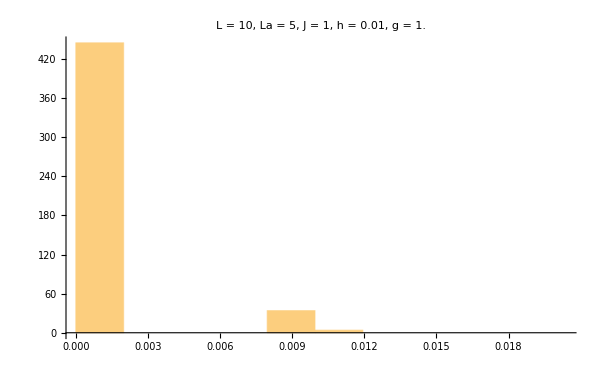

```mathematica
ListPlot[{Transpose[{newall[[All,1]],eigenvecdiag}],Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Gray,PointSize[0.009]],Directive[Blue,PointSize[0.005]],Directive[Red,PointSize[0.005]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]]
MeanLevelSpacingRatio[Sort[eveneigenval]]
MeanLevelSpacingRatio[Sort[oddeigenval]]
Histogram[Differences[Sort[eveneigenval]],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],ImageSize->600]
Histogram[Differences[Sort[oddeigenval]],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],ImageSize->600]
```

```mathematica
allstates={};
Do[
state=RandomQubitState[];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@Table[state,L/2]],Flatten[KroneckerProduct@@Table[state,L/2]]]];
AppendTo[allstates,evenini];
,{i,1000}];
iprs=ParallelTable[Total[Abs[Conjugate[allvecs].i]^4],{i,allstates}];
sorted=SortBy[Transpose[{iprs,allstates}],First];
evenini=sorted[[1,2]];
```

```mathematica
tlist=Table[10^i,{i,-2,10,0.0025}];
tlist//Length
```

4801

```mathematica
entro=ParallelTable[evensvn[L,La,Lb,evenini,eveneigenval,eveneigenvec,Beven,t],{t,tlist},DistributedContexts->Full];
inieigen=Beven.Conjugate[eveneigenvec].(Transpose[Beven].evenini);
sdiagonal=Total[Map[VNentropy,Chop[Eigenvalues[MatrixPartialTrace[Dyad[inieigen],2,{2^(L/2),2^(L/2)}]]]]];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Black,Dashed]];
diagplot=LogLinearPlot[sdiagonal,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]];
```

```mathematica
plot1=ListLogLinearPlot[Transpose[{tlist,entro}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["+ RPS",Black,30]},PlotStyle->{Directive[Blue,Opacity[0.5]]}];
```

```mathematica
productstate2=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,productstate2},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,productstate2}],First];
productstates=data[[1,2]];
svntproduct=ParallelTable[{t,svn[L,La,Lb,productstates,allvals,allvecs,t]},{t,tlist},DistributedContexts->Full];
```

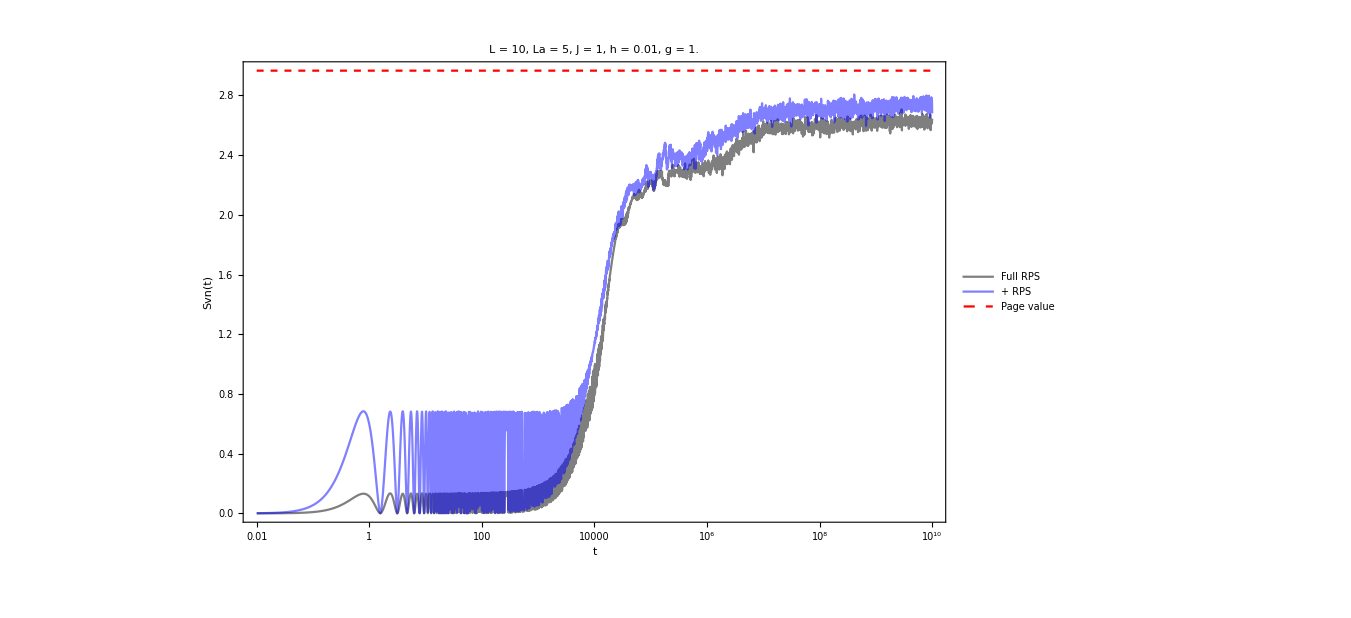

```mathematica
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Red],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Full RPS",Black,30]},PlotStyle->{Directive[Black,Opacity[0.5]]}];Show[{svnplots,plot1,pageplot},PlotRange->All]
```

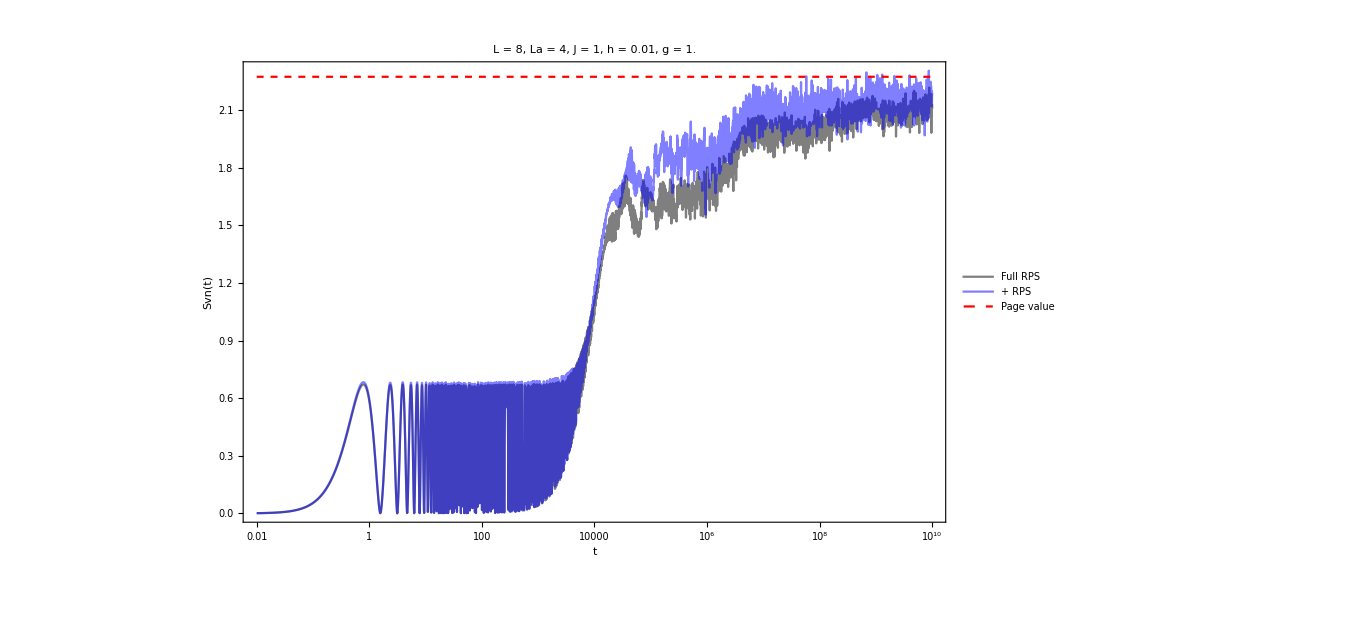

```mathematica
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Red],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Full RPS",Black,30]},PlotStyle->{Directive[Black,Opacity[0.5]]}];Show[{svnplots,plot1,pageplot},PlotRange->All]
```

# Translation sectors

```mathematica
L=10; (*Length of the spin chain*)
dim=2^L; (*Dimension of the Hilbert space*)
basisStates=IntegerDigits[Range[0,dim-1],2,L];
TranslateState[state_List]:=RotateLeft[state];
orbits={};
visited=Association[];
Do[If[!KeyExistsQ[visited,state],orbit=NestList[TranslateState,state,L-1];
orbit=DeleteDuplicates[orbit];
(*Mark all states in the orbit as visited*)Scan[(visited[#]=True)&,orbit];
AppendTo[orbits,orbit];],{state,basisStates}];
momentumEigenstates={};
Do[orbitSize=Length[orbit];
Do[k=2 Pi m/orbitSize;
stateSum=ConstantArray[0,dim];
Do[translatedState=Nest[TranslateState,orbit[[1]],n];
index=Position[basisStates,translatedState][[1,1]];
stateSum[[index]]+=Exp[-I k n];,{n,0,orbitSize-1}];
normalizedState=stateSum/Norm[stateSum];
AppendTo[momentumEigenstates,{k,normalizedState}];,{m,0,orbitSize-1}];,{orbit,orbits}];
ks=First/@momentumEigenstates;
perm=OrderingBy[momentumEigenstates,First];
sortedKEigen=ks[[perm]];
sortedStates=(Last/@momentumEigenstates)[[perm]];
sortedPairs=Transpose[{sortedKEigen,sortedStates}];
posByK=GroupBy[Range@Length[sortedKEigen],sortedKEigen[[#]]&];
blocks={};
Do[
AppendTo[blocks,sortedStates[[i[[1]];;i[[-1]]]]];
,{i,posByK}];
Table[Dimensions[i],{i,blocks}]
```

{{108,1024},{99,1024},{105,1024},{99,1024},{105,1024},{100,1024},{105,1024},{99,1024},{105,1024},{99,1024}}

```mathematica
J=5;
h=1;
g=1;
H=IsingNNClosedHamiltonian[h,g,J,L];
```

```mathematica
La=L/2;
Lb=L-La;
```

```mathematica
data={};
Do[
Beven=Transpose[j];
Heven=ConjugateTranspose[Beven].H.Beven;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
AppendTo[data,Transpose[{eveneigenval,eveneigenvecdiag}]];
,{j,blocks}];
```

```mathematica
ListAnimate[Table[ListPlot[i,PlotRange->All,ImageSize->700,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLegends->DeleteDuplicates[ks],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]],{i,data}],AnimationRunning->False]
```

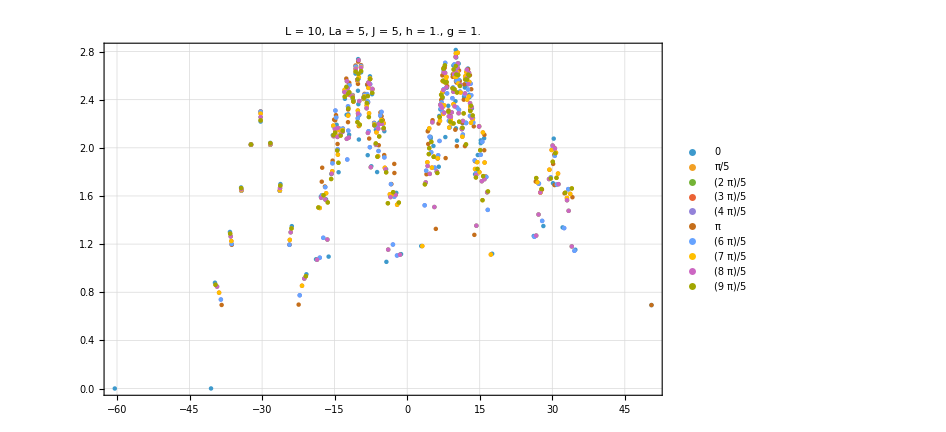

```mathematica
ListPlot[data,PlotRange->All,ImageSize->700,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLegends->DeleteDuplicates[ks],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]]
```

```mathematica
allstates={};
Do[
state=RandomQubitState[];
evenini=Flatten[KroneckerProduct[Flatten[KroneckerProduct@@Table[state,L/2]],Flatten[KroneckerProduct@@Table[state,L/2]]]];
AppendTo[allstates,evenini];
,{i,1000}];
```

```mathematica
iprs=ParallelTable[Total[Abs[Conjugate[allvecs].i]^4],{i,allstates}];
```

```mathematica
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

```mathematica
sorted=SortBy[Transpose[{iprs,allstates}],First];
```

```mathematica
evenini=sorted[[1,2]];
```

```mathematica
tlist=Table[10^i,{i,-2,3,0.0025}];
tlist//Length
```

2001

```mathematica
entro=ParallelTable[evensvn[L,La,Lb,evenini,eveneigenval,eveneigenvec,Beven,t],{t,tlist},DistributedContexts->Full];
inieigen=Beven.Conjugate[eveneigenvec].(Transpose[Beven].evenini);
sdiagonal=Total[Map[VNentropy,Chop[Eigenvalues[MatrixPartialTrace[Dyad[inieigen],2,{2^(L/2),2^(L/2)}]]]]];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Black,Dashed]];
diagplot=LogLinearPlot[sdiagonal,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]];
```

```mathematica
plot1=ListLogLinearPlot[Transpose[{tlist,entro}],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["+ RPS",Black,30]},PlotStyle->{Directive[Blue,Opacity[0.5]]}];
```

```mathematica
productstate2=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,productstate2},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,productstate2}],First];
productstates=data[[1,2]];
svntproduct=ParallelTable[{t,svn[L,La,Lb,productstates,allvals,allvecs,t]},{t,tlist},DistributedContexts->Full];
```

```mathematica
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Red],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[N[g]],35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Single RPS",Black,30]},PlotStyle->{Directive[Black,Opacity[0.5]]}];
Show[{svnplots,plot1,pageplot}]
```